# q q̄→μ μ in EW theory (SM ): Gauge box

File con calcolo tracce: moltiplico per le cariche e calcolo traccia. nei file prec. facevo contrario

provo a moltiplicare subito per propagatore prima del calcolo della traccia

### PROCESS:

```mathematica
CKM = IndexDelta;
Neglect[MU] = Neglect[MU2] = 0;
Neglect[MM] = Neglect[MM2] = 0;
process ={-F[3, {1}], F[3, {1}]} -> {-F[2, {2}], F[2, {2}]} ;

SetOptions[InsertFields,  Model -> "SM",InsertionLevel->{Particles}, Restrictions -> NoLightFHCoupling];
(*SetOptions[CalcFeynAmp,PaVeReduce->True];*)
SetOptions[CreateFeynAmp, GaugeRules -> {GaugeXi[Z] -> ZGAUGE, GaugeXi[A] -> AGAUGE,
 GaugeXi[W] -> WGAUGE} ];
```

## SM: Feynman rules and diagrams

Definisco valori di cariche e masse sostituite poi nei passaggi finali

```mathematica
CHARGESZl={QZLl->-1,QZUl->2/3,QZDl->-1/3,I3D->-1/2,I3L->-1/2,I3N->1/2,I3U->1/2};
CHARGESZr={QZLr->-1,QZUr->2/3,QZDr->-1/3};
CHARGESphl={QLl->-1,QUl->2/3,QDl->-1/3};
CHARGESphr={QLr->-1,QUr->2/3,QDr->-1/3};
MASSES={MU->0,MU2->0,MM->0,MM2->0,MD->0,MD2->0,S+T+U->0}
```

{MU→0,MU2→0,MM→0,MM2→0,MD→0,MD2→0,S+T+U→0}

```mathematica
(*GENERALIZZAZIONE CARICHE/ISOSPIN PER CASO SM*)
coupling[x_]:=Module[{Mcouplin,chargenuZ,chargelepZ,chargeupZ,chargedownZ,n,m,chargenup,chargelep,chargedown,chargeup},

Mcouplin=M$CouplingMatrices;
(*____________________________  Z COUPLING  ______________________________*)
(*neutrino*)
chargenuZ[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[2]])==rhs_]:=
lhs==(rhs/.{
	dZZZ1-> 2 I3N dZZZ1,
	1/(2 CW SW)->I3N/(CW SW),
	EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
	

});
chargenuZ[other_]=other;
Mcouplin=chargenuZ/@Mcouplin;

(*lepton*)
chargelepZ[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3L*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			SW/CW->-QZLl SW/CW,
			(-1/2+SW^2)->(I3L-QZLl*SW^2),
			dZAZ1->- QLl dZAZ1 (*CT misto gamma Z*)
			},
		rhsR/.{
		SW/CW->-QZLr SW/CW,
		dZAZ1->- QLr dZAZ1 (*CT misto gamma Z*)
		}
});
chargelepZ[other_]=other;
Mcouplin=chargelepZ/@Mcouplin;

(*q up*)
chargeupZ[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3U*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(1/2-2/3SW^2)->(I3U-QZUl*SW^2),
			
			dZAZ1->3/2 QUl dZAZ1,(*CT misto gamma Z: − δ [g1,g2] QU δZ(γZ)/2*)
			-2/3->-QZUl},
		rhsR/.{
			-dZAZ1 /3->-QUr*dZAZ1 /2, (*CT misto gamma Z*)
			-1/3 I*EL->-QZUr/2 I*EL,
			-2/3*I->-QZUr*I,
			-2/3->-QZUr,
			-SW /(3*CW)->-QZUr*SW /(2*CW)}
});
chargeupZ[other_]=other;
Mcouplin=chargeupZ/@Mcouplin;

(*q down*)
chargedownZ[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{
			-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3D*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),
			dZAZ1->-3 QDl dZAZ1, (*CT misto gamma Z*)
			1/3->-QZDl},
			
		rhsR/.{
			dZZZ1->- 3 QZDr*dZZZ1 ,
			dZAZ1->- 3 QDr*dZAZ1 ,(*CT misto gamma Z*)
			1/3 I*EL->-QZDr I*EL,
			1/3*I->-QZDr*I,
			1/3->-QZDr,
			SW /(3*CW)->-QZDr*SW /(CW)}
});
chargedownZ[other_]=other;
Mcouplin=chargedownZ/@Mcouplin;

(*____________________________  GAMMA COUPLING  ___________________________*)
(*neutrino*)
chargenup[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[1]])==rhs_]:=
lhs==(rhs/.{
		EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
});
chargenup[other_]=other;
Mcouplin=chargenup/@Mcouplin;
(*lepton*)
chargelep[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+SW^2)->(I3L-QZLl*SW^2)/-QLl,(*CT misto gamma Z*)
			I->-QLl*I,
			1/2*I->-1/2 QLl*I
},
			
		rhsR/.{dZZA1->- QZLr dZZA1/-QLr,(*CT misto gamma Z*)
		I->-QLr*I,
			1/2*I->-1/2 QLr*I
		}
});
chargelep[other_]=other;
Mcouplin=chargelep/@Mcouplin;

(*q up*)
chargeup[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(1/2-2/3SW^2)->(I3U-QZUl*SW^2),(*CT misto gamma Z*)
			-2/3->-QUl,
			-2/3*I->-QUl*I},
			
		rhsR/.{dZZA1->3/2 QZUr dZZA1,(*CT misto gamma Z*)
		-2/3->-QUr,
		-2/3*I->-QUr*I}
});
chargeup[other_]=other;
Mcouplin=chargeup/@Mcouplin;

(*q down*)
chargedown[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),(*CT misto gamma Z*)
			1/3->-QDl,
			1/3*I->-QDl*I
			},
							
	rhsR/.{ dZZA1->-3 QZDr dZZA1,(*CT misto gamma Z*)
			1/3->-QDr,
			1/3*I->-QDr*I}
});
chargedown[other_]=other;
Mcouplin=chargedown/@Mcouplin;

Mcouplin
];
```

```mathematica
InitializeModel["SM",
ModelEdit :>{
M$ClassesDescription=M$ClassesDescription//.{(-Charge)->QL Charge,(2/3Charge)->QU Charge,(-1/3Charge)->QD Charge},
M$CouplingMatrices=coupling[M$CouplingMatrices]}

];
```

loading generic model file /home/arianna/Documenti/FeynArts-3.11/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/arianna/Documenti/FeynArts-3.11/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

## Feynman Diagrams

## Tree Level

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 18 field point(s)

in total: 2 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams



FeynArtsGraphics[][([1] | [2])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

```mathematica
tops = CreateTopologies[0, 2 -> 2];
ins = InsertFields[tops, process];
Paint[ins,ColumnsXRows->{2,1},Numbering->Simple,
SheetHeader->None,ImageSize->{512,256}]
born1=CreateFeynAmp[ins];
```

## Self Energies

```mathematica
tops2 = CreateTopologies[1, 2 -> 2, SelfEnergiesOnly];
ins2 = InsertFields[tops2, process];
ins2 = DiagramSelect[ins2, FreeQ[#, Field[5|6] -> S]&];
Paint[ins2,ColumnsXRows->{11,7},Numbering->Simple,
SheetHeader->None,ImageSize->{1212,756}]
selfff=CreateFeynAmp[ins2];
```

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 10 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 65 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

Restoring 18 field point(s)

in total: 75 Particles insertions

> Top. 1 aebe/cfdf/egfggg.m, 0 diagrams

> Top. 2 aebe/cfdf/egfhghgh.m, 0 diagrams

-Graphics-

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5] | [6] | [7] | [8] | [9] | [10] | [11]
[12] | [13] | [14] | [15] | [16] | [17] | [18] | [19] | [20] | [21] | [22]
[23] | [24] | [25] | [26] | [27] | [28] | [29] | [30] | [31] | [32] | [33]
[34] | [35] | [36] | [37] | [38] | [39] | [40] | [41] | [42] | [43] | [44]
[45] | [46] | [47] | [48] | [49] | [50] | [51] | [52] | [53] | [54] | [55]
[56] | [57] | [58] | [59] | [60] | [61] | [62] | [63] | [64] | [65] | [66]
[67] | [68] | [69] | [70] | [71] | [72] | [73] | [74] | [75] | Null | Null)]

creating amplitudes at level(s) {Particles}

> Top. 1: 10 Particles amplitudes

> Top. 2: 65 Particles amplitudes

in total: 75 Particles amplitudes

## Vertices

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 7 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 8 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

Restoring 18 field point(s)

in total: 15 Particles insertions

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 2 aebf/cgdg/ghefehfh.m, 0 diagrams

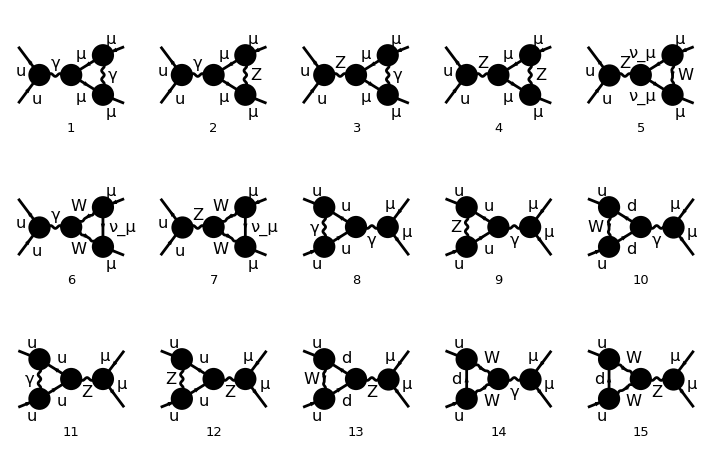

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5]
[6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15])]

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5]
[6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15])]

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

```mathematica
tops4 = CreateTopologies[1, 2 -> 2, TrianglesOnly];
ins4 = InsertFields[tops4, process];
ins4 = DiagramSelect[ins4, FreeQ[#, Field[5] -> S]&];
Paint[ins4,ColumnsXRows->{5,3},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
verttt=CreateFeynAmp[ins4];
```

## Boxes

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 4 Particles insertions

> Top. 8: 5 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

Restoring 18 field point(s)

in total: 9 Particles insertions

> Top. 1 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 2 aebf/cgdh/efehfggh.m, 0 diagrams

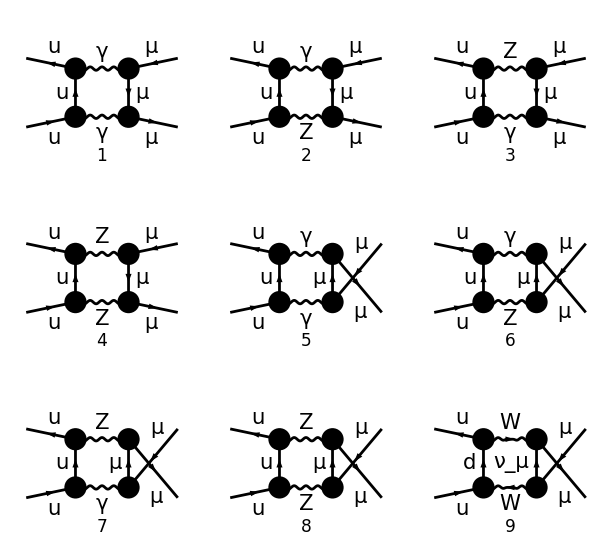

FeynArtsGraphics[][([1] | [2] | [3]
[4] | [5] | [6]
[7] | [8] | [9])]

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

> Top. 2: 5 Particles amplitudes

in total: 9 Particles amplitudes

```mathematica
tops5 = CreateTopologies[1, 2 -> 2, BoxesOnly];
ins5 = InsertFields[tops5, process];
Paint[ins5,ColumnsXRows->{3,3},Numbering->Simple,
SheetHeader->None,ImageSize->{612,556}]
box1=  CreateFeynAmp[ins5];
```

## Counterterms (CT)

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 2 Particles insertions

> Top. 8: 4 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

Restoring 18 field point(s)

in total: 8 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebe/cfdf/gegf.m, 0 diagrams

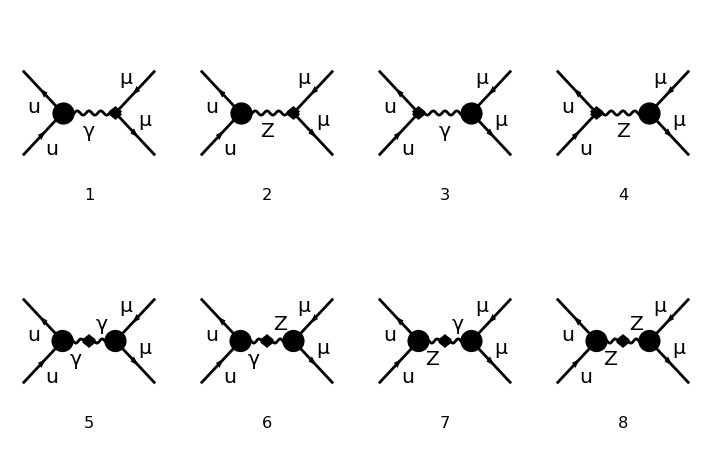

FeynArtsGraphics[][([1] | [2] | [3] | [4]
[5] | [6] | [7] | [8])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 4 Particles amplitudes

in total: 8 Particles amplitudes

```mathematica
tops1 = CreateCTTopologies[1, 2 -> 2,
  ExcludeTopologies -> {TadpoleCTs,WFCorrectionCTs (*loop counterterms*)}];
ins1 = InsertFields[tops1, process];
Paint[ins1,ColumnsXRows->{4,2},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
counter = CreateFeynAmp[ins1];
```

## BOX

ampiezzabox . ampiezzaborn*

#### Classificazione

```mathematica
(*in input mettere box1*)
boxtable[box_]:=Module[{b1,b2,b3,samediag,b4,tden,uden,boxcl0,boxcl1},

(*primo metodo: topologie*)
b1=Table[
Which[MemberQ[Part[box,{i}][[1,1]],Topology==1,Infinity],T,
MemberQ[Part[box,{i}][[1,1]],Topology==2,Infinity],U,
True,Print["not identified"]],(*identificazione diagrammi t con particelle gamma/Z/W in base ai valori delle cariche negli stati finali, l'ordine è up,down. Il caso WW è per esclusione*)

{i,1,Length[box1]}];

(*secondo metodo*)
(*
tden=PropagatorDenominator[Plus[FourMomentum[Incoming,2],FourMomentum[Internal,1],Times[-1,FourMomentum[Outgoing,2]]],0];
uden=PropagatorDenominator[Plus[FourMomentum[Incoming,2],FourMomentum[Internal,1],Times[-1,FourMomentum[Outgoing,1]]],0];


boxcl0=Table[boxcl1[i]=Union[Cases[Part[box,{i}][[1,3]]/.MASSES,_FeynAmpDenominator,Infinity]/.FeynAmpDenominator->Sequence],
{i,1,Length[box]}];
Print[boxcl0];

b1=Table[
Which[MemberQ[boxcl1[i],tden,Infinity],T,
MemberQ[boxcl1[i],uden,Infinity],U,True,Null](*,
DeleteCases[boxcl1[i],uden|tden,Infinity]*),
{i,1,Length[box1]}];
*)
(*******************)

b2=Table[
Which[b1[[i]]===T,
{Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QZLl,Infinity],Z,
True,W],
Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QZLl,Infinity],Z,
True,W]},
b1[[i]]===U,

{Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QZLl,Infinity],Z,
True,W],
Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QZLl,Infinity],Z,
True,W]}
,
True,Print["not identified"]](*identificazione diagrammi t con topology 1 e u con topology 2*)
,(*identificazione diagrammi t con particelle gamma/Z/W in base ai valori delle cariche negli stati finali, l'ordine è up,down. Il caso WW è per esclusione*)

{i,1,Length[box]}];
b3=Table[{i,b1[[i]],b2[[i]]},{i,1,Length[box]}];
Print[b3];
samediag=Gather[b3,Last[#1]==Last[#2]&];
b4=Table[{couple[i]==Last[samediag[[i,1]]],bbox[i]=Cases[samediag[[i]],_Integer,{2}]},{i,1,Length[samediag]}];(*couples:diag t , diag u*)


b4
];
```

```mathematica
boxtable[box1]
```

{{1,T,{γ,γ}},{2,T,{γ,Z}},{3,T,{Z,γ}},{4,T,{Z,Z}},{5,U,{γ,γ}},{6,U,{γ,Z}},{7,U,{Z,γ}},{8,U,{Z,Z}},{9,U,{W,W}}}

{{couple[1]=={γ,γ},{1,5}},{couple[2]=={γ,Z},{2,6}},{couple[3]=={Z,γ},{3,7}},{couple[4]=={Z,Z},{4,8}},{couple[5]=={W,W},{9}}}

```mathematica
Table[totbbox[i]={Part[box1,{bbox[i][[1]]}][[1,3]],Part[box1,{bbox[i][[2]]}][[1,3]]},{i,1,4}];
totbbox[5]=Part[box1,{bbox[5][[1]]}][[1,3]];
```

```mathematica
(*set variabili semplificate*)
mzg=Times[MZ,Power[ZGAUGE,Rational[1,2]]];
mwg=Times[MW,Power[WGAUGE,Rational[1,2]]];
P1=FourMomentum[Incoming,1];
P2=FourMomentum[Incoming,2];
Q1=FourMomentum[Internal,1];
K1=FourMomentum[Outgoing,1];
K2=FourMomentum[Outgoing,2];
```

### Caso box generico:

METTERE MANUALMENTE: totbbox[i] e 1 per fotone e 2 per z per born diagram

```mathematica
tboxzz=totbbox[4][[1]]//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
uboxzz=totbbox[4][[2]]//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
wwbox=totbbox[5]//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
```

```mathematica
tboxzz=tboxzz/.FourMomentum[Internal,1]->Times[-1,FourMomentum[Internal,1]]
uboxzz=uboxzz/.FourMomentum[Internal,1]->Times[-1,FourMomentum[Internal,1]]
wwbox=wwbox/.FourMomentum[Internal,1]->Times[-1,FourMomentum[Internal,1]];
```

1/(16 π^4)ⅈ v̄[p1,0].((ⅈ EL (I3U-QZUl SW2) ga[Lor1].om_-)/(CW SW)-(ⅈ EL QZUr SW ga[Lor1].om_+)/CW).gs[q1].((ⅈ EL (I3U-QZUl SW2) IndexDelta[Col1,Col2] ga[Lor3].om_-)/(CW SW)-(ⅈ EL QZUr SW IndexDelta[Col1,Col2] ga[Lor3].om_+)/CW).u[p2,0] ū[k2,0].((ⅈ EL (I3L-QZLl SW2) ga[Lor4].om_-)/(CW SW)-(ⅈ EL QZLr SW ga[Lor4].om_+)/CW).gs[-(p2)+q1+k2].((ⅈ EL (I3L-QZLl SW2) ga[Lor2].om_-)/(CW SW)-(ⅈ EL QZLr SW ga[Lor2].om_+)/CW).v[k1,0] ((1-ZGAUGE)^2 FeynAmpDenominator[1/(-MZ2+(p2-q1)^2),1/(-MZ2 ZGAUGE+(p2-q1)^2),1/(q1)^2,1/(p2-q1-k2)^2,1/(-MZ2+(p2-q1-k1-k2)^2),1/(-MZ2 ZGAUGE+(p2-q1-k1-k2)^2)] (p2-q1)[Lor4] (-(p2)+q1)[Lor3] (p2-q1-k1-k2)[Lor1] (-(p2)+q1+k1+k2)[Lor2]+(1-ZGAUGE) FeynAmpDenominator[1/(-MZ2+(p2-q1)^2),1/(-MZ2 ZGAUGE+(p2-q1)^2),1/(q1)^2,1/(p2-q1-k2)^2,1/(-MZ2+(p2-q1-k1-k2)^2)] (p2-q1)[Lor4] (-(p2)+q1)[Lor3] g[Lor1,Lor2]+(1-ZGAUGE) FeynAmpDenominator[1/(-MZ2+(p2-q1)^2),1/(q1)^2,1/(p2-q1-k2)^2,1/(-MZ2+(p2-q1-k1-k2)^2),1/(-MZ2 ZGAUGE+(p2-q1-k1-k2)^2)] (p2-q1-k1-k2)[Lor1] (-(p2)+q1+k1+k2)[Lor2] g[Lor3,Lor4]+FeynAmpDenominator[1/(-MZ2+(p2-q1)^2),1/(q1)^2,1/(p2-q1-k2)^2,1/(-MZ2+(p2-q1-k1-k2)^2)] g[Lor1,Lor2] g[Lor3,Lor4]) SumOver[Col1,3,External] SumOver[Col2,3,External]

1/(16 π^4)ⅈ v̄[p1,0].((ⅈ EL (I3U-QZUl SW2) ga[Lor1].om_-)/(CW SW)-(ⅈ EL QZUr SW ga[Lor1].om_+)/CW).gs[q1].((ⅈ EL (I3U-QZUl SW2) IndexDelta[Col1,Col2] ga[Lor3].om_-)/(CW SW)-(ⅈ EL QZUr SW IndexDelta[Col1,Col2] ga[Lor3].om_+)/CW).u[p2,0] ū[k2,0].((ⅈ EL (I3L-QZLl SW2) ga[Lor2].om_-)/(CW SW)-(ⅈ EL QZLr SW ga[Lor2].om_+)/CW).gs[p2-q1-k1].((ⅈ EL (I3L-QZLl SW2) ga[Lor4].om_-)/(CW SW)-(ⅈ EL QZLr SW ga[Lor4].om_+)/CW).v[k1,0] ((1-ZGAUGE)^2 FeynAmpDenominator[1/(-MZ2+(p2-q1)^2),1/(-MZ2 ZGAUGE+(p2-q1)^2),1/(q1)^2,1/(p2-q1-k1)^2,1/(-MZ2+(p2-q1-k1-k2)^2),1/(-MZ2 ZGAUGE+(p2-q1-k1-k2)^2)] (p2-q1)[Lor4] (-(p2)+q1)[Lor3] (p2-q1-k1-k2)[Lor1] (-(p2)+q1+k1+k2)[Lor2]+(1-ZGAUGE) FeynAmpDenominator[1/(-MZ2+(p2-q1)^2),1/(-MZ2 ZGAUGE+(p2-q1)^2),1/(q1)^2,1/(p2-q1-k1)^2,1/(-MZ2+(p2-q1-k1-k2)^2)] (p2-q1)[Lor4] (-(p2)+q1)[Lor3] g[Lor1,Lor2]+(1-ZGAUGE) FeynAmpDenominator[1/(-MZ2+(p2-q1)^2),1/(q1)^2,1/(p2-q1-k1)^2,1/(-MZ2+(p2-q1-k1-k2)^2),1/(-MZ2 ZGAUGE+(p2-q1-k1-k2)^2)] (p2-q1-k1-k2)[Lor1] (-(p2)+q1+k1+k2)[Lor2] g[Lor3,Lor4]+FeynAmpDenominator[1/(-MZ2+(p2-q1)^2),1/(q1)^2,1/(p2-q1-k1)^2,1/(-MZ2+(p2-q1-k1-k2)^2)] g[Lor1,Lor2] g[Lor3,Lor4]) SumOver[Col1,3,External] SumOver[Col2,3,External]

```mathematica
(*funzione per semplificare propagatori*)
numer[x__ PropagatorDenominator[p_,MZ] PropagatorDenominator[p_,mzg]]:=numer[x/(MZ^2-mzg^2)(PropagatorDenominator[p,MZ]-PropagatorDenominator[p,mzg])];
numerw[x__ PropagatorDenominator[p_,MW] PropagatorDenominator[p_,mwg]]:=numerw[x/(MW^2-mwg^2)(PropagatorDenominator[p,MW]-PropagatorDenominator[p,mwg])];
```

```mathematica
(*BORN*)
born=Part[born1,{1}][[1,3]]//.{Index[Lorentz, 1]->Index[Lorentz, bn1],
Index[Lorentz, 2]->Index[Lorentz, bn2]}//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
bornchains=DeleteCases[Cases[born,_FermionChain,Infinity],_IndexDelta,Infinity];
conjbornchains=CONJ/@Reverse[bornchains,{2}]/.{I->-I,-I->I}
(*colour matrix*)
colourborn=Union[Cases[born,_SumOver|_IndexDelta,Infinity]]
(*born propagators*)
bornpropag=DeleteCases[born, _SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times;
bornpropag2=Collect[numer/@%/.numer->Sequence//Simplify,
PropagatorDenominator[x_,mzg],Simplify]//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_,c___]->1/(a^2-b^2)^c
```

{CONJ[v̄[p2,0].(ⅈ EL QUl ga[Lorbn1].om_-+ⅈ EL QUr ga[Lorbn1].om_+).u[p1,0]],CONJ[ū[k1,0].(ⅈ EL QLl ga[Lorbn2].om_-+ⅈ EL QLr ga[Lorbn2].om_+).v[k2,0]]}

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

((-1+AGAUGE) (SP[k1,Lorbn1]+SP[k2,Lorbn1]) (SP[k1,Lorbn2]+SP[k2,Lorbn2]))/(k1+k2)^4+SP[Lorbn1,Lorbn2]/(k1+k2)^2

#### colour trace

```mathematica
(*LOOP DIAGRAM*)

colourf[diag_]:=Module[{input2,fermionchain},
diagram=diag;
(*trace closed fermion loop(if any)*)
tr=Cases[diagram,_MatrixTrace,Infinity];
(*fermionchain without tr and with external particles masses->0*)
input2=DeleteCases[diagram,_MatrixTrace,Infinity]//.MASSES;
fermionchain=Cases[input2,_FermionChain,Infinity];
(*colour traces*)
sunt=Cases[Collect[fermionchain,_SUNT,Simplify],_SUNT| _IndexDelta,Infinity];
trsunt=Cases[Collect[tr,_SUNT,Simplify],_SUNT| _IndexDelta,Infinity];(*SUNT in tr*)
sumover=Cases[input2,_SumOver,Infinity];
colour=Join[sunt,trsunt,sumover,colourborn];

colour
];
```

```mathematica
colourf[tboxzz]
colourf[uboxzz]
colourf[wwbox]
colourf[Part[selfff,{4}]]
```

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External],IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External],IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External],IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

«1 more identical outputs»

#### Semplificazione propagatori

Divisione in termini dipendenti da gauge e indipendenti

```mathematica
(*box t*)
tnumerat=DeleteCases[tboxzz, _MatrixTrace |_SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times//Simplify
(*box u*)
unumerat=DeleteCases[uboxzz, _MatrixTrace |_SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times//Simplify
(*box w*)
wnumerat=DeleteCases[wwbox, _MatrixTrace |_SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times//Simplify
```

1/(16 π^4)ⅈ 1/(-MZ2+(p2-q1)^2) (g[Lor3,Lor4]+(-(p2)+q1)[Lor3] ((p2-q1)[Lor4]+ZGAUGE (-(p2)+q1)[Lor4]) 1/(-MZ2 ZGAUGE+(p2-q1)^2)) 1/(q1)^2 1/(p2-q1-k2)^2 1/(-MZ2+(p2-q1-k1-k2)^2) (g[Lor1,Lor2]+((p2-q1-k1-k2)[Lor1]+ZGAUGE (-(p2)+q1+k1+k2)[Lor1]) (-(p2)+q1+k1+k2)[Lor2] 1/(-MZ2 ZGAUGE+(p2-q1-k1-k2)^2))

1/(16 π^4)ⅈ 1/(-MZ2+(p2-q1)^2) (g[Lor3,Lor4]+(-(p2)+q1)[Lor3] ((p2-q1)[Lor4]+ZGAUGE (-(p2)+q1)[Lor4]) 1/(-MZ2 ZGAUGE+(p2-q1)^2)) 1/(q1)^2 1/(p2-q1-k1)^2 1/(-MZ2+(p2-q1-k1-k2)^2) (g[Lor1,Lor2]+((p2-q1-k1-k2)[Lor1]+ZGAUGE (-(p2)+q1+k1+k2)[Lor1]) (-(p2)+q1+k1+k2)[Lor2] 1/(-MZ2 ZGAUGE+(p2-q1-k1-k2)^2))

1/(16 π^4)ⅈ 1/(-MW2+(p2-q1)^2) (g[Lor3,Lor4]+(-(p2)+q1)[Lor3] ((p2-q1)[Lor4]+WGAUGE (-(p2)+q1)[Lor4]) 1/(-MW2 WGAUGE+(p2-q1)^2)) 1/(q1)^2 1/(p2-q1-k1)^2 1/(-MW2+(p2-q1-k1-k2)^2) (g[Lor1,Lor2]+((p2-q1-k1-k2)[Lor1]+WGAUGE (-(p2)+q1+k1+k2)[Lor1]) (-(p2)+q1+k1+k2)[Lor2] 1/(-MW2 WGAUGE+(p2-q1-k1-k2)^2))

```mathematica
(*prove semplificaz propagatore generico*)
sempp[propag_]:=Module[{t1,t11,t111,t1111,t2,t22,t222,t2222,tnumerat1,tnumerat2,t1w,t11w,t111w,t1111w,t2w,t22w,t222w,t2222w,tnumerat1w,tnumerat2w},
propagatore=propag;
tnn=Select[propagatore,MemberQ[#,ZGAUGE|MZ,Infinity]&];(*seleziona i termini contenenti ZGAUGE oppure massa MZ*)
tnn2=Select[propagatore,FreeQ[#,ZGAUGE|MZ,Infinity]&];(*seleziona i termini restanti, passaggio intermedio*)
	tnnw=Select[tnn2,MemberQ[#,WGAUGE|MW,Infinity]&];(*seleziona i termini contenenti WGAUGE oppure massa MW in tnn2*)
	tnnrest=Select[tnn2,FreeQ[#,WGAUGE|MW,Infinity]&];(*seleziona i termini restanti*)
(*propagatore=tnn*tnnw*tnnrest*)

(*ZGAUGE*)
Which[Length[tnn]===2,(*caso di diagrammi con γ e Z*)
	t1=tnn//Expand;
	t11=numer/@t1/.numer->Sequence//Simplify;
	t111=Collect[t11,PropagatorDenominator[x_,mzg],FullSimplify]//.ZGAUGE->Zm1+1//.FourVector[a__]:>Distribute[FourVector[a]];
	t1111=Collect[t111,Zm1,Simplify]//.FourVector[a__,b_]-FourVector[a__,b_]->0//.Zm1->ZGAUGE-1;
	tnumerat1=t1111//.FourVector[a_, Index[w__]]+FourVector[b_, Index[w__]] ->FourVector[a + b, Index[w]];
	totnum=tnumerat1,

	Length[tnn]>2,(*caso con 2 Z*)
		t1=tnn[[1;;Length[tnn]/2]]//Expand;
		t11=numer/@t1/.numer->Sequence//Simplify;
		t111=Collect[t11,PropagatorDenominator[x_,mzg],FullSimplify]//.ZGAUGE->Zm1+1//.FourVector[a__]:>Distribute[FourVector[a]];
		t1111=Collect[t111,Zm1,Simplify]//.FourVector[a__,b_]-FourVector[a__,b_]->0//.Zm1->ZGAUGE-1;
		tnumerat1=t1111//.FourVector[a_, Index[w__]]+FourVector[b_, Index[w__]]->FourVector[a + b, Index[w]];

		t2=tnn[[Length[tnn]/2+1;;Length[tnn]]]//Expand;
		t22=numer/@t2/.numer->Sequence//Simplify;
		t222=Collect[t22,PropagatorDenominator[x_,mzg],FullSimplify]//.ZGAUGE->Zm1+1//.FourVector[a__]:>Distribute[FourVector[a]];
		t2222=Collect[t222,Zm1,Simplify]//.FourVector[a__,b_]-FourVector[a__,b_]->0//.Zm1->ZGAUGE-1;
		tnumerat2=t2222//.FourVector[a_, Index[w__]]+FourVector[b_, Index[w__]]->FourVector[a + b, Index[w]];
		totnum=tnumerat1*tnumerat2,

	True,
		totnum=1];

(*WGAUGE*)
Which[Length[tnnw]===2,(*caso di diagrammi con un solo W*)
		t1w=tnnw//Expand;
		t11w=numerw/@t1w/.numerw->Sequence//Simplify;
		t111w=Collect[t11w,PropagatorDenominator[x_,mwg],FullSimplify]//.ZGAUGE->Zm1+1//.FourVector[a__]:>Distribute[FourVector[a]];
		t1111w=Collect[t111w,Zm1,Simplify]//.FourVector[a__,b_]-FourVector[a__,b_]->0//.Zm1->ZGAUGE-1;
		tnumerat1w=t1111w//.FourVector[a_, Index[w__]]+FourVector[b_, Index[w__]] ->FourVector[a + b, Index[w]];
		totnum1=tnumerat1w,

	Length[tnnw]>2,(*caso con 2 W*)
		t1w=tnnw[[1;;Length[tnnw]/2]]//Expand;
		t11w=numerw/@t1w/.numerw->Sequence//Simplify;
		t111w=Collect[t11w,PropagatorDenominator[x_,mwg],FullSimplify]//.WGAUGE->Zm1+1//.FourVector[a__]:>Distribute[FourVector[a]];
		t1111w=Collect[t111w,Zm1,Simplify]//.FourVector[a__,b_]-FourVector[a__,b_]->0//.Zm1->WGAUGE-1;
		tnumerat1w=t1111w//.FourVector[a_, Index[w__]]+FourVector[b_, Index[w__]] ->FourVector[a + b, Index[w]];

	t2w=tnnw[[Length[tnnw]/2+1;;Length[tnnw]]]//Expand;
	t22w=numerw/@t2w/.numerw->Sequence//Simplify;
	t222w=Collect[t22w,PropagatorDenominator[x_,mwg],FullSimplify]//.WGAUGE->Zm1+1//.FourVector[a__]:>Distribute[FourVector[a]];
	t2222w=Collect[t222w,Zm1,Simplify]//.FourVector[a__,b_]-FourVector[a__,b_]->0//.Zm1->WGAUGE-1;
	tnumerat2w=t2222w//.FourVector[a_, Index[w__]]+FourVector[b_, Index[w__]] ->FourVector[a + b, Index[w]];
	totnum1=tnumerat1w*tnumerat2w,

	True,
		totnum1=1];


propagtot=totnum*totnum1*tnnrest];
```

```mathematica
tpropag=sempp[tnumerat]
upropag=sempp[unumerat]
wpropag=sempp[wnumerat]
```

1/(16 MZ2^2 π^4)ⅈ ((p2-q1)[Lor3] (-(p2)+q1)[Lor4] 1/(-MZ2+(p2-q1)^2)+MZ2 g[Lor3,Lor4] 1/(-MZ2+(p2-q1)^2)+(-(p2)+q1)[Lor3] (-(p2)+q1)[Lor4] 1/(-MZ2 ZGAUGE+(p2-q1)^2)) 1/(q1)^2 1/(p2-q1-k2)^2 ((p2-q1-k1-k2)[Lor1] (-(p2)+q1+k1+k2)[Lor2] 1/(-MZ2+(p2-q1-k1-k2)^2)+MZ2 g[Lor1,Lor2] 1/(-MZ2+(p2-q1-k1-k2)^2)+(-(p2)+q1+k1+k2)[Lor1] (-(p2)+q1+k1+k2)[Lor2] 1/(-MZ2 ZGAUGE+(p2-q1-k1-k2)^2))

1/(16 MZ2^2 π^4)ⅈ ((p2-q1)[Lor3] (-(p2)+q1)[Lor4] 1/(-MZ2+(p2-q1)^2)+MZ2 g[Lor3,Lor4] 1/(-MZ2+(p2-q1)^2)+(-(p2)+q1)[Lor3] (-(p2)+q1)[Lor4] 1/(-MZ2 ZGAUGE+(p2-q1)^2)) 1/(q1)^2 1/(p2-q1-k1)^2 ((p2-q1-k1-k2)[Lor1] (-(p2)+q1+k1+k2)[Lor2] 1/(-MZ2+(p2-q1-k1-k2)^2)+MZ2 g[Lor1,Lor2] 1/(-MZ2+(p2-q1-k1-k2)^2)+(-(p2)+q1+k1+k2)[Lor1] (-(p2)+q1+k1+k2)[Lor2] 1/(-MZ2 ZGAUGE+(p2-q1-k1-k2)^2))

1/(16 MW2^2 π^4)ⅈ ((p2-q1)[Lor3] (-(p2)+q1)[Lor4] 1/(-MW2+(p2-q1)^2)+MW2 g[Lor3,Lor4] 1/(-MW2+(p2-q1)^2)+(-(p2)+q1)[Lor3] (-(p2)+q1)[Lor4] 1/(-MW2 WGAUGE+(p2-q1)^2)) 1/(q1)^2 1/(p2-q1-k1)^2 ((p2-q1-k1-k2)[Lor1] (-(p2)+q1+k1+k2)[Lor2] 1/(-MW2+(p2-q1-k1-k2)^2)+MW2 g[Lor1,Lor2] 1/(-MW2+(p2-q1-k1-k2)^2)+(-(p2)+q1+k1+k2)[Lor1] (-(p2)+q1+k1+k2)[Lor2] 1/(-MW2 WGAUGE+(p2-q1-k1-k2)^2))

```mathematica
nn=6;
denomt=tnumerat[[nn]]/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)
denomu=unumerat[[nn]]/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)
```

1/(p2-q1-k2)^2

1/(p2-q1-k1)^2

```mathematica
(*propagatore born*)
bornpropag2
(*propagatore box, parte in comune fra t e u. propagatore box W*)
propagatT=tnumerat[[nn]];
propagatU=unumerat[[nn]];

ptot=DeleteCases[tpropag,propagatT,Infinity]+DeleteCases[upropag,propagatU,Infinity]//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_,c___]->1/(a^2-b^2)^c
ptotw=DeleteCases[wpropag,propagatU,Infinity]//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_,c___]->1/(a^2-b^2)^c
```

((-1+AGAUGE) (SP[k1,Lorbn1]+SP[k2,Lorbn1]) (SP[k1,Lorbn2]+SP[k2,Lorbn2]))/(k1+k2)^4+SP[Lorbn1,Lorbn2]/(k1+k2)^2

1/(8 MZ2^2 π^4 (q1)^2)ⅈ (((SP[p2,Lor1]-SP[q1,Lor1]-SP[k1,Lor1]-SP[k2,Lor1]) (-SP[p2,Lor2]+SP[q1,Lor2]+SP[k1,Lor2]+SP[k2,Lor2]))/(-MZ2+(p2-q1-k1-k2)^2)+((-SP[p2,Lor1]+SP[q1,Lor1]+SP[k1,Lor1]+SP[k2,Lor1]) (-SP[p2,Lor2]+SP[q1,Lor2]+SP[k1,Lor2]+SP[k2,Lor2]))/(-MZ2 ZGAUGE+(p2-q1-k1-k2)^2)+(MZ2 SP[Lor1,Lor2])/(-MZ2+(p2-q1-k1-k2)^2)) (((SP[p2,Lor3]-SP[q1,Lor3]) (-SP[p2,Lor4]+SP[q1,Lor4]))/(-MZ2+(p2-q1)^2)+((-SP[p2,Lor3]+SP[q1,Lor3]) (-SP[p2,Lor4]+SP[q1,Lor4]))/(-MZ2 ZGAUGE+(p2-q1)^2)+(MZ2 SP[Lor3,Lor4])/(-MZ2+(p2-q1)^2))

1/(16 MW2^2 π^4 (q1)^2)ⅈ (((SP[p2,Lor1]-SP[q1,Lor1]-SP[k1,Lor1]-SP[k2,Lor1]) (-SP[p2,Lor2]+SP[q1,Lor2]+SP[k1,Lor2]+SP[k2,Lor2]))/(-MW2+(p2-q1-k1-k2)^2)+((-SP[p2,Lor1]+SP[q1,Lor1]+SP[k1,Lor1]+SP[k2,Lor1]) (-SP[p2,Lor2]+SP[q1,Lor2]+SP[k1,Lor2]+SP[k2,Lor2]))/(-MW2 WGAUGE+(p2-q1-k1-k2)^2)+(MW2 SP[Lor1,Lor2])/(-MW2+(p2-q1-k1-k2)^2)) (((SP[p2,Lor3]-SP[q1,Lor3]) (-SP[p2,Lor4]+SP[q1,Lor4]))/(-MW2+(p2-q1)^2)+((-SP[p2,Lor3]+SP[q1,Lor3]) (-SP[p2,Lor4]+SP[q1,Lor4]))/(-MW2 WGAUGE+(p2-q1)^2)+(MW2 SP[Lor3,Lor4])/(-MW2+(p2-q1)^2))

#### Trace

```mathematica
(*  naive anticommuting gamma5 definitions   *)
myTr[a_,b_] := 4 SP[a,b];
myTr[x__] := Module[{lista,ultima,menouno,menodue,coefficienti,nuovetracce,
                     risultato, i},
		    lista = {x};
                    ultima = lista[[-1]];
		    menouno = Delete[lista,-1];
		    menodue = Table[ Delete[ menouno, i], {i,1,Length[menouno]}];
		    coefficienti = Table[ (-1)^(i+1) SP[ultima,menouno[[i]] ],
                                          {i,1,Length[menouno]}];
		    nuovetracce = Map[ Apply[ myTr, # ] &, menodue];

                    risultato = coefficienti.nuovetracce;
                    risultato
 ] /; FreeQ[{x},G5] ;
```

```mathematica
myTr[G5,G5] = 4;
myTr[z___,-G5]:=-myTr[z,G5];
myTr[s___,MM,u___]:=MM myTr[s,u];
myTr[x_,G5] = 0;
myTr[x_,y_,G5] = 0;
myTr[x_,y_,z_,G5] = 0;
myTr[x__,G5] := 0 /; OddQ[Length[{x}]] && FreeQ[{x},G5] ;
myTr[a___,G5,b___,G5,c___] := (-1)^Length[{b}]*myTr[a,b,c] /; FreeQ[{b},G5] ;
myTr[a___,G5,b__] := (-1)^Length[{b}]*myTr[a,b,G5] /; FreeQ[Union[{a},{b}],G5] ;
myTr[a1_,a2_,a3_,a4_,G5] =- 4 I myEps[a1,a2,a3,a4];
(* myTr[x___,a1_,a2_,a3_,a4_,a5_,a6_,G5] := Module[ {lista,ultima,menouno,menodue,coefficienti,nuovetracce,
                     risultato, i},
  index = Unique[a];
  risultato = myTr[x,a1,a2,a3,a6,G5] SP[a4,a5]-
              myTr[x,a1,a2,a3,a5,G5] SP[a4,a6]+
              myTr[x,a1,a2,a3,a4,G5] SP[a5,a6]+
  I  myTr[x,a1,a2,a3,DiracMatrix[Index[Lorentz,index]]] myEps[a4,a5,a6,Index[Lorentz,index]]; 
  risultato
 ]  /; FreeQ[Union[{x},{a1,a2,a3,a4,a5,a6}],G5] ;*)
```

```mathematica
(*funzioni prodotto scalare e levicivita*)
SetAttributes[SP,Orderless];
SP/:SP[Index[u__],Index[v__]] SP[p_,Index[u__]] := SP[p,Index[v]];
SP/:SP[a_,Index[mu__]]^2 := SP[a,a];
SP/:SP[a_,Index[mu__]] SP[b_,Index[mu__]] := SP[a,b];
SP/:SP[Index[mu__],Index[mu__]] = d;
SP/:SP[Index[mu__],Index[nu__]]^2 = d;
SP/:SP[-b_,a_]:=-SP[b,a];
SP/:SP[DiracSlash[w_],x_]:=SP[w,x];
SP/:SP[DiracMatrix[w_],x_]:=SP[w,x];
(*levicivita product. 4 indices (d->4)*)
myEps/:myEps[a__]^2:=-Expand@Det@Outer[SP,{a},{a}];
myEps/:myEps[a__] myEps[b__]:=-Expand@Det@Outer[SP,{a},{b}];
```

```mathematica
SP/:SP[P1,P1]:=0;
SP/:SP[P2,P2]:=0;
SP/:SP[K2,K2]:=0;
SP/:SP[K1,K1]:=0;
SP/:SP[P1,P2]:=S/2;
SP/: SP[K1,K2]:=S/2;
SP/: SP[P1,K1]:=(-T)/2;
SP/: SP[P2,K2]:=(-T)/2; 
SP/:SP[P1,K2]:=(-U)/2; 
SP/:SP[P2,K1]:=(-U)/2;
SP/:SP[Q1,Q1]:=Q1^2;
```

```mathematica
(*PROPRIETÀ MYEPS*)
myEps/:myEps[t___,DiracSlash[w_],x___]:=myEps[t,w,x];
myEps/:myEps[t___,DiracMatrix[w_],x___]:=myEps[t,w,x];
myEps /: myEps[a___,Index[Lorentz,mu_],b___] SP[p_,Index[Lorentz,mu_]] := myEps[a,p,b]; 
myEps[a___,b_,c___,b_,d___] := 0
```

```mathematica
move2[a___,ChiralityProjector[pm_],dm:MM|-MM,b___]:=move2[a,dm,ChiralityProjector[pm],b];
move2[a___,ChiralityProjector[pm_],dm:_DiracMatrix|_DiracSlash,b___]:=move2[a,dm,ChiralityProjector[-pm],b];
move2[a___,ChiralityProjector[x_],ChiralityProjector[y_],b___]:=0/;x≠y;
move2[a___,ChiralityProjector[x_],ChiralityProjector[y_],b___]:=move2[a,ChiralityProjector[x],b]/;x==y;
move2[a___,1,b___]:=move2[a,b];
move2[a___,DiracSlash[-FourMomentum[p__]],b___]:=-move2[a,DiracSlash[FourMomentum[p]],b];
(*NOTA: ANTICOMMUTAZIONE IN D-DIMENSIONI *)
```

```mathematica
trr[s___,MM,u___]:=MM trr[s,u];
trr[s___,-MM,u___]:=-MM trr[s,u];
```

```mathematica
(*calcolo traccia*)
traces[statoi_,statof_,propp_]:=Module[{tr0f,tr1i,tr2i,tr3i,tr1f,tr2f,tr3f},

(*trace:*)
traceff4[x___, DiracSpinor[z:K2|P2,w_], DiracSpinor[z:K2|P2,w_],y___]:=traceff4[x,(DiracSlash[z]+w),y];
traceff4[ DiracSpinor[z:K2|P2,w_],x__,DiracSpinor[z:K2|P2,w_]]:=traceff4[(DiracSlash[z]+w),x];
traceff4[x___, DiracSpinor[z:K1|P1,w_], DiracSpinor[z:K1|P1,w_],y___]:=traceff4[x,(DiracSlash[z]-w),y];
traceff4[ DiracSpinor[z:K1|P1,w_],x__,DiracSpinor[z:K1|P1,w_]]:=traceff4[(DiracSlash[z]-w),x];
traceff4[a___,-G5,b___]:=- traceff4[a,G5,b];

chargetot=List[chi,chf]//.genericCHZ//.{QUr->QU,QUl->QU,QLl->QL,QLr->QL};
(*stato i*)
tr1i=Table[traceff4[statoi[[i]]/.List->Sequence],{i,1,Length[statoi]}]//.traceff4->move2;(*sposto proiettori in fondo*)
tr1i=tr1i*chargetot[[1]]//.List->Plus//Simplify;(*prova*)
tr2i=Map[Distribute,1/2 tr1i//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity]//Expand;(*sostituisco om+- con espressioni G5 esplicite*)

(*tr3i=tr2i//.move2->TR//.TR->myTr//Expand;espando e calcolo traccia*)

(*tr4ie=Select[tr2i,MemberQ[#,G5,Infinity]&]//.move2[DiracSlash[a__],b___,DiracSlash[a__],m:-G5|G5]->0/.move2[a___,-G5]->-move2[a,G5]//.move2->TR//.TR->myTr//Expand;*)

tr4ie=Select[tr2i,MemberQ[#,G5,Infinity]&]//.move2[DiracSlash[a__],b__,DiracSlash[a__],m:-G5|G5]->0/.move2[a___,-G5]->-move2[a,G5]//.move2->TR//.diractracefeync//.TR->myTr//Expand;


tr4ine=Select[tr2i,FreeQ[#,G5,Infinity]&]/.move2->TR//.TR->myTr//Expand;
tr5i=tr4ie+tr4ine;

Print["stato i ",1/2 tr1i//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)}];

(*stato f*)
tr0f=Table[traceff4[statof[[i]]/.List->Sequence],{i,1,Length[statof]}];
tr1f=Replace[Table[{Distribute[tr0f[[i]]]},{i,1,Length[tr0f]}],Plus->Sequence,{2},Heads->True]//.traceff4->move2;
tr1f=tr1f*chargetot[[2]]//.List->Plus//Simplify;
tr2f=Map[Distribute,1/2 tr1f//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity];

(*tr3f=tr2f//.move2->trr//.trr->TR//.TR->myTr//Expand;*)

tr3f=tr2f*bornpropag2*propp//.SOST//Expand;
tr4f=tr3f//.move2[a___,DiracMatrix[Index[Lorentz,b_]],c___]*SP[FourMomentum[f__],Index[Lorentz,b_]]->move2[a,DiracSlash[FourMomentum[f]],c];
(*tr4fe=Select[tr4f,MemberQ[#,G5,Infinity]&]//.move2[DiracSlash[a__],b___,DiracSlash[a__],m:-G5|G5]->0/.move2[a___,-G5]->-move2[a,G5]//.move2->TR//.TR->myTr//Expand;*)

tr4fe=Select[tr4f,MemberQ[#,G5,Infinity]&]//.move2[DiracSlash[a__],b__,DiracSlash[a__],m:-G5|G5]->0/.move2[a___,-G5]->-move2[a,G5]//.move2->TR//.diractracefeync//.TR->myTr//Expand;
tr4fne=Select[tr4f,FreeQ[#,G5,Infinity]&]/.move2->trr//.trr->TR//.TR->myTr//Expand;
tr5f=tr4fe+tr4fne;

Print["stato f ",1/2 tr1f//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)}];

Return[{tr5i,tr5f}]

];
```

```mathematica
diractracefeync=TR[muu_,nuu_,rhoo_,sigg_,dell_,tauu_,G5]->-4 I myEps[nuu,rhoo,sigg,tauu]SP[dell,muu]-4 I myEps[muu,nuu,rhoo,sigg]SP[dell,tauu]-4 I myEps[dell,nuu,rhoo,sigg]SP[muu,tauu]-4 I myEps[dell,muu,sigg,tauu]SP[nuu,rhoo]+4 I myEps[dell,muu,rhoo,tauu]SP[nuu,sigg]-4 I myEps[dell,muu,nuu,tauu]SP[rhoo,sigg]
```

TR[muu_,nuu_,rhoo_,sigg_,dell_,tauu_,G5]→-4 ⅈ myEps[nuu,rhoo,sigg,tauu] SP[dell,muu]-4 ⅈ myEps[muu,nuu,rhoo,sigg] SP[dell,tauu]-4 ⅈ myEps[dell,nuu,rhoo,sigg] SP[muu,tauu]-4 ⅈ myEps[dell,muu,sigg,tauu] SP[nuu,rhoo]+4 ⅈ myEps[dell,muu,rhoo,tauu] SP[nuu,sigg]-4 ⅈ myEps[dell,muu,nuu,tauu] SP[rhoo,sigg]

```mathematica
TR[DiracMatrix[Index[Lorentz,1]],DiracMatrix[Index[Lorentz,2]],DiracMatrix[Index[Lorentz,3]],DiracMatrix[Index[Lorentz,4]],DiracMatrix[Index[Lorentz,5]],DiracMatrix[Index[Lorentz,6]],G5]//.diractracefeync
```

-4 ⅈ myEps[Lor2,Lor3,Lor4,Lor6] SP[Lor1,Lor5]-4 ⅈ myEps[Lor5,Lor2,Lor3,Lor4] SP[Lor1,Lor6]-4 ⅈ myEps[Lor5,Lor1,Lor4,Lor6] SP[Lor2,Lor3]+4 ⅈ myEps[Lor5,Lor1,Lor3,Lor6] SP[Lor2,Lor4]-4 ⅈ myEps[Lor5,Lor1,Lor2,Lor6] SP[Lor3,Lor4]-4 ⅈ myEps[Lor1,Lor2,Lor3,Lor4] SP[Lor5,Lor6]

```mathematica
TR[a___,m_,b__,m_,c___] := (-1)^Length[{b}] d TR[a,b,c]+Sum[ma={b}; tmp=Delete[ma,i]; 
(-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;Head[m]===DiracMatrix &&  FreeQ[{b},G5]; 
TR[a___,m_,b__,m_,c___] := Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[P1]&&  FreeQ[{b},G5]; 
TR[a___,m_,b__,m_,c___] := Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[P2] && FreeQ[{b},G5]; 
TR[a___,m_,b__,m_,c___] := Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[K1]&&  FreeQ[{b},G5]; 
TR[a___,m_,b__,m_,c___] :=Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[K2]&&  FreeQ[{b},G5]; 

TR[]:=1;
TR[s___,MM,u___]:=MM TR[s,u];
TR[s___,-MM,u___]:=-MM TR[s,u];
(*semplification diraslash*)
TR[x___,DiracSlash[-z_],y___]:=-TR[x,DiracSlash[z],y];
(*trd2[x___,DiracSlash[s_],DiracMatrix[t_],DiracSlash[s_],y___]:=2*SP[t,s]*trd2[x,DiracSlash[s],y]-trd2[x,DiracSlash[s],DiracSlash[s],DiracMatrix[t],y];
trd2[x___,DiracSlash[s_],DiracSlash[t_],DiracSlash[s_],y___]:=2*SP[t,s]*trd2[x,DiracSlash[s],y]-trd2[x,DiracSlash[s],DiracSlash[s],DiracSlash[t],y];*)

TR[x___,DiracSlash[P1],DiracSlash[P1],y___]:=0;
TR[x___,DiracSlash[P2],DiracSlash[P2],y___]:=0;
TR[x___,DiracSlash[K1],DiracSlash[K1],y___]:=0;
TR[x___,DiracSlash[K2],DiracSlash[K2],y___]:=0;
TR[a___,DiracMatrix[Index[Lorentz,m_]],DiracMatrix[Index[Lorentz,m_]], b___] := d TR[a,b];
       
TR[a_,b_]= 4 SP[a,b];
```

```mathematica
Select[tr4f,MemberQ[#,G5,Infinity]&]//.move2[DiracSlash[a__],b___,DiracSlash[a__],m:-G5|G5]->0//.move2->TR//.TR->myTr//Expand
```

(4 Alfa EL I3L^2 π QL T myEps[Lor2,k1,Lorbn1,Lor4])/(CW2 DK1K2 SW2)+(8 Alfa EL I3L^2 π QL myEps[Lor2,k1,Lorbn1,k2] SP[p2,Lor4])/(CW2 DK1K2 SW2)+(8 Alfa EL I3L^2 π QL myEps[Lor2,k1,Lorbn1,Lor4] SP[q1,k2])/(CW2 DK1K2 SW2)-(8 Alfa EL I3L^2 π QL myEps[Lor2,k1,Lorbn1,k2] SP[q1,Lor4])/(CW2 DK1K2 SW2)-(8 Alfa EL I3L^2 π QL myEps[k2,Lor4,p2,Lorbn1] SP[k1,Lor2])/(CW2 DK1K2 SW2)+(8 Alfa EL I3L^2 π QL myEps[k2,Lor4,q1,Lorbn1] SP[k1,Lor2])/(CW2 DK1K2 SW2)-(8 Alfa EL I3L^2 π QL myEps[k2,Lor4,p2,Lor2] SP[k1,Lorbn1])/(CW2 DK1K2 SW2)+(8 Alfa EL I3L^2 π QL myEps[k2,Lor4,q1,Lor2] SP[k1,Lorbn1])/(CW2 DK1K2 SW2)+(16 Alfa EL I3L^2 π QL myEps[k2,Lor2,k1,Lorbn1] SP[k2,Lor4])/(CW2 DK1K2 SW2)+(8 Alfa EL I3L^2 π QL myEps[Lor2,k1,Lorbn1,p2] SP[k2,Lor4])/(CW2 DK1K2 SW2)-(8 Alfa EL I3L^2 π QL myEps[Lor2,k1,Lorbn1,q1] SP[k2,Lor4])/(CW2 DK1K2 SW2)+(8 Alfa EL I3L^2 π QL myEps[k2,Lor4,p2,k1] SP[Lor2,Lorbn1])/(CW2 DK1K2 SW2)-(8 Alfa EL I3L^2 π QL myEps[k2,Lor4,q1,k1] SP[Lor2,Lorbn1])/(CW2 DK1K2 SW2)

```mathematica
Select[tr4f,MemberQ[#,G5,Infinity]&]//.move2[DiracSlash[a__],b___,DiracSlash[a__],m:-G5|G5]->0/.move2[a___,-G5]->-move2[a,G5]//.move2->TR//.diractracefeync//.TR->myTr//Expand
```

-(4 Alfa EL I3L^2 π QL S myEps[Lor4,p2,Lor2,Lorbn1])/(CW2 DK1K2 SW2)+(4 Alfa EL I3L^2 π QL S myEps[Lor4,q1,Lor2,Lorbn1])/(CW2 DK1K2 SW2)-(8 Alfa EL I3L^2 π QL myEps[k1,k2,Lor4,Lorbn1] SP[p2,Lor2])/(CW2 DK1K2 SW2)-(8 Alfa EL I3L^2 π QL myEps[k1,k2,Lor2,Lorbn1] SP[p2,Lor4])/(CW2 DK1K2 SW2)+(8 Alfa EL I3L^2 π QL myEps[k1,k2,Lor4,Lorbn1] SP[q1,Lor2])/(CW2 DK1K2 SW2)+(8 Alfa EL I3L^2 π QL myEps[k1,k2,Lor2,Lorbn1] SP[q1,Lor4])/(CW2 DK1K2 SW2)-(8 Alfa EL I3L^2 π QL myEps[k2,Lor4,p2,Lor2] SP[k1,Lorbn1])/(CW2 DK1K2 SW2)+(8 Alfa EL I3L^2 π QL myEps[k2,Lor4,q1,Lor2] SP[k1,Lorbn1])/(CW2 DK1K2 SW2)+(16 Alfa EL I3L^2 π QL myEps[k2,Lor2,k1,Lorbn1] SP[k2,Lor4])/(CW2 DK1K2 SW2)-(8 Alfa EL I3L^2 π QL myEps[k1,Lor4,p2,Lor2] SP[k2,Lorbn1])/(CW2 DK1K2 SW2)+(8 Alfa EL I3L^2 π QL myEps[k1,Lor4,q1,Lor2] SP[k2,Lorbn1])/(CW2 DK1K2 SW2)+(8 Alfa EL I3L^2 π QL myEps[k1,k2,p2,Lorbn1] SP[Lor2,Lor4])/(CW2 DK1K2 SW2)-(8 Alfa EL I3L^2 π QL myEps[k1,k2,q1,Lorbn1] SP[Lor2,Lor4])/(CW2 DK1K2 SW2)

```mathematica
(*input->diag=loop diagram *)
fermiontrace[diag_]:=Module[{tborn1,tborn2,hb,hbc,tborn3i,tborn3ic,tborn3f,tborn3fc,fermionchain,sti,sti1,tbi,tbic,tbi2,tbi3,tbi3c,stf,stf1,tbf,tbfc,tbf2,tbf3,tbf3c},
(*****BORN*****)
tborn1=Table[Map[Distribute,conjbornchains,3][[i]],{i,1,2}];
tborn2=Apply[List,tborn1,{1}]/.CONJ->Sequence;
(*seleziono termini per calcolo traccia e cariche*)
hb=Table[Table[Cases[tborn2[[j,i]],_NonCommutative,Infinity],{i,1,Length[tborn2[[j]]]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence,{j,1,2}];
hbc=Table[Table[DeleteCases[tborn2[[j,i]],_NonCommutative,Infinity],{i,1,Length[tborn2[[j]]]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence,{j,1,2}];
(*STATO I*)
tborn3i=Flatten[Select[hb,MemberQ[#,DiracSpinor[P1,_],Infinity]&],1];
tborn3ic=Flatten[Select[hbc,MemberQ[#,QZUl|QUl,Infinity]&],1];(*charges/coupling*)
(*STATO F*)
tborn3f=Flatten[Select[hb,MemberQ[#,DiracSpinor[K1,_],Infinity]&],1];
tborn3fc=Flatten[Select[hbc,MemberQ[#,QZLl|QLl,Infinity]&],1];(*charges/coupling*)

(*****LOOP DIAGRAM*****)
(*trace closed fermion loop(if any)*)
tr=Cases[diag,_MatrixTrace,Infinity];
(*fermionchain without tr and with external particles masses->0*)
input=DeleteCases[diag,_MatrixTrace,Infinity]//.MASSES;
(*fermionchain part for trace computation*)
fermionchain=DeleteCases[Cases[input,_FermionChain,Infinity],_SUNT|_IndexDelta,Infinity];
(*select fermionchain, expand sums, split state i/f*)
tab1=Table[Distribute[fermionchain[[i]]],{i,1,2}];
(*STATO I*)
sti=Select[tab1,MemberQ[#,DiracSpinor[P1,_],Infinity]&];(*select stato i*)
If[MemberQ[sti,Plus[FermionChain[__],_],Infinity],sti1=Flatten[Apply[List,sti,{1}],1],sti1=sti];(*suddivide in lista se ha piu elementi*)
(*seleziono termini per calcolo traccia e cariche*)
tbi=Table[Cases[sti1[[i]],_NonCommutative,Infinity],{i,1,Length[sti1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbic=Table[DeleteCases[sti1[[i]],_NonCommutative,Infinity],{i,1,Length[sti1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;

tbi2=Table[move2@@tbi[[i]],{i,1,Length[tbi]}]//.move2->List;(*sposto proiettori in fondo a destra con anticommutazione*)
tbi3=DeleteCases[tbi2,0,1];
tbi3c=Delete[tbic,Position[tbi2,0,{1}]];(*semplificazione se ci sono dei termini nulli dove ho om- om+ *)
(*union diag*born*)
stati=Flatten[Table[{Join[tbi3[[i]],tborn3i[[1]]],Join[tbi3[[i]],tborn3i[[2]]]},{i,1,Length[tbi3]}],1];
chi=Flatten[Table[{Join[tbi3c[[i]],tborn3ic[[1]]],Join[tbi3c[[i]],tborn3ic[[2]]]},{i,1,Length[tbi3c]}],1]//.FermionChain->Times;

(*STATO F*)(*procedimento analogo a STATO I*)
stf=Select[tab1,MemberQ[#,DiracSpinor[K2,_],Infinity]&];
If[MemberQ[stf,Plus[FermionChain[__],_],Infinity],stf1=Flatten[Apply[List,stf,{1}],1],stf1=stf];
tbf=Table[Cases[stf1[[i]],_NonCommutative,Infinity],{i,1,Length[stf1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbfc=Table[DeleteCases[stf1[[i]],_NonCommutative,Infinity],{i,1,Length[stf1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbf2=Replace[Table[Distribute[tbf[[i]]//.List->f],{i,1,Length[tbf]}],Plus->Sequence,{2},Heads->True]//.f->move2;
tbf3=DeleteCases[tbf2,0,1]//.move2->List;
If[FreeQ[tbf2,MM,Infinity],
tbf3c=Delete[tbfc,Position[tbf2,0,{1}]],
tbf3c=tbfc];(*semplificazione se ci sono dei termini nulli dove ho om- om+ *)
statf=Flatten[Table[{Join[tbf3[[i]],tborn3f[[1]]],Join[tbf3[[i]],tborn3f[[2]]]},{i,1,Length[tbf3]}],1];
chf=Flatten[Table[{Join[tbf3c[[i]],tborn3fc[[1]]],Join[tbf3c[[i]],tborn3fc[[2]]]},{i,1,Length[tbf3c]}],1]//.FermionChain->Times;

Print["trace closed fermion loop(if any): ",tr];
Return[{stati,statf}]
];
```

```mathematica
genericCHZ={QZLl->QLl,QZUl->QUl,QZDl->QDl,QZLr->QLr,QZUr->QUr,QZDr->QDr};
sostituzione={SP[Q1,Q1]->Q1^2};
```

```mathematica
(*box 1*)
```

```mathematica
pgaugeaa=Select[ptot//Expand,MemberQ[#,AGAUGE^2,Infinity]&]//.P1->K1+K2-P2//.SP[x__]:>Distribute[SP[x]];
```

```mathematica
pgaugea=Select[ptot//Expand,MemberQ[#,AGAUGE,Infinity]&&FreeQ[#,AGAUGE^2,Infinity]&]//.P1->K1+K2-P2//.SP[x__]:>Distribute[SP[x]];
```

```mathematica
(*box 2*)(*box 3*)
```

```mathematica
pgaugeaz=Select[ptot//Expand,MemberQ[#,AGAUGE,Infinity]&&MemberQ[#,ZGAUGE,Infinity]&]//.P1->K1+K2-P2//.SP[x__]:>Distribute[SP[x]];
```

```mathematica
pgaugeaNz=Select[ptot//Expand,MemberQ[#,AGAUGE,Infinity]&&FreeQ[#,ZGAUGE,Infinity]&]//.P1->K1+K2-P2//.SP[x__]:>Distribute[SP[x]];
```

```mathematica
pgaugezNa=Select[ptot//Expand,MemberQ[#,ZGAUGE,Infinity]&&FreeQ[#,AGAUGE,Infinity]&]//.P1->K1+K2-P2//.SP[x__]:>Distribute[SP[x]];
```

```mathematica
(*box 4*)
```

```mathematica
pgaugezz=Select[ptot//Expand,Count[#,ZGAUGE,Infinity]===2&]//.P1->K1+K2-P2//.SP[x__]:>Distribute[SP[x]];
```

```mathematica
pgaugez=Select[ptot//Expand,Count[#,ZGAUGE,Infinity]===1&]//.P1->K1+K2-P2//.SP[x__]:>Distribute[SP[x]];
```

```mathematica
boxtt=traces[fermiontrace[tboxzz][[1]],fermiontrace[tboxzz][[2]],pgaugez];
```

trace closed fermion loop(if any): {}

trace closed fermion loop(if any): {}

stato i -1/(CW2 SW2)2 ⅈ Alfa EL π QU ((I3U-QU SW2)^2 move2[gs[p1],ga[Lor1],gs[q1],ga[Lor3],gs[p2],ga[Lorbn1],1-G5]+QU^2 SW2^2 move2[gs[p1],ga[Lor1],gs[q1],ga[Lor3],gs[p2],ga[Lorbn1],1+G5])

stato f -1/(CW2 SW2)2 ⅈ Alfa EL π QL ((I3L-QL SW2)^2 move2[gs[k2],ga[Lor4],gs[-(p2)+q1+k2],ga[Lor2],gs[k1],ga[Lorbn2],1-G5]+QL^2 SW2^2 move2[gs[k2],ga[Lor4],gs[-(p2)+q1+k2],ga[Lor2],gs[k1],ga[Lorbn2],1+G5])

```mathematica
boxuu=traces[fermiontrace[uboxzz][[1]],fermiontrace[uboxzz][[2]],pgaugez];
```

trace closed fermion loop(if any): {}

trace closed fermion loop(if any): {}

stato i -1/(CW2 SW2)2 ⅈ Alfa EL π QU ((I3U-QU SW2)^2 move2[gs[p1],ga[Lor1],gs[q1],ga[Lor3],gs[p2],ga[Lorbn1],1-G5]+QU^2 SW2^2 move2[gs[p1],ga[Lor1],gs[q1],ga[Lor3],gs[p2],ga[Lorbn1],1+G5])

stato f -1/(CW2 SW2)2 ⅈ Alfa EL π QL ((I3L-QL SW2)^2 move2[gs[k2],ga[Lor2],gs[p2-q1-k1],ga[Lor4],gs[k1],ga[Lorbn2],1-G5]+QL^2 SW2^2 move2[gs[k2],ga[Lor2],gs[p2-q1-k1],ga[Lor4],gs[k1],ga[Lorbn2],1+G5])

## Semplificazioni/sostituzioni

```mathematica
(*regole di sostituzione dei denominatori e regole inverse*)
SOST={-MZ2+(P2-Q1)^2->DMZQ1P2,-MZ2 ZGAUGE+(P2-Q1)^2->DMZGQ1P2,
-MW2+(P2-Q1)^2->DMWQ1P2,-MW2 WGAUGE+(P2-Q1)^2->DMWGQ1P2,
-MZ2+(K1+K2)^2->DMZK1K2,-MZ2 ZGAUGE+(K1+K2)^2->DMZGK1K2,
-MZ2+(P2-Q1-K1-K2)^2->DMZQ1P2K1K2,-MZ2 ZGAUGE+(P2-Q1-K1-K2)^2->DMZGQ1P2K1K2,
-MW2+(P2-Q1-K1-K2)^2->DMWQ1P2K1K2,-MW2 WGAUGE+(P2-Q1-K1-K2)^2->DMWGQ1P2K1K2,
MZ2-(K1+K2)^2->-DMZK1K2,MZ2 ZGAUGE-(K1+K2)^2->-DMZGK1K2,
MZ2-(P2-Q1)^2->-DMZQ1P2,MZ2 ZGAUGE-(P2-Q1)^2->-DMZGQ1P2,
MZ2-(P2-Q1-K1-K2)^2->-DMZQ1P2K1K2,MZ2 ZGAUGE-(P2-Q1-K1-K2)^2->-DMZGQ1P2K1K2,
MW2-(P2-Q1)^2->-DMWQ1P2,MW2 WGAUGE-(P2-Q1)^2->-DMWGQ1P2,
MW2-(P2-Q1-K1-K2)^2->-DMWQ1P2K1K2,MW2 WGAUGE-(P2-Q1-K1-K2)^2->-DMWGQ1P2K1K2,

(P2-Q1-K1-K2)->Sqrt[DQ1P2K1K2],
(P2-Q1-K2)->Sqrt[DQ1P2K2],
(P2-Q1-K1)->Sqrt[DQ1P2K1],
(P2-Q1)->Sqrt[DQ1P2],
(K1+K2)->Sqrt[DK1K2],
Q1^n_/;EvenQ[n]->DQ1^(n/2),Q1^n_/;OddQ[n]&&n<0->DQ1^((n+1)/2)1/Q1,Q1^n_/;OddQ[n]&&n>0->DQ1^((n-1)/2)Q1,
-Q1^n_/;EvenQ[n]->-DQ1^(n/2),-Q1^n_/;OddQ[n]->-DQ1^((n-1)/2)Q1};

SOSTINV={DMZQ1P2->-MZ2+(P2-Q1)^2,DMZGQ1P2->-MZ2 ZGAUGE+(P2-Q1)^2,
DMWQ1P2->-MW2+(P2-Q1)^2,DMWGQ1P2->-MW2 WGAUGE+(P2-Q1)^2,
DMZK1K2->-MZ2+(K1+K2)^2,DMZGK1K2->-MZ2 ZGAUGE+(K1+K2)^2,
DMZQ1P2K1K2->-MZ2+(P2-Q1-K1-K2)^2,DMZGQ1P2K1K2->-MZ2 ZGAUGE+(P2-Q1-K1-K2)^2,
DMWQ1P2K1K2->-MW2+(P2-Q1-K1-K2)^2,DMWGQ1P2K1K2->-MW2 WGAUGE+(P2-Q1-K1-K2)^2,

DQ1P2K1K2->(P2-Q1-K1-K2)^2,
DQ1P2K2->(P2-Q1-K2)^2,
DQ1P2K1->(P2-Q1-K1)^2,
DQ1P2->(P2-Q1)^2,
DK1K2->(K1+K2)^2,
DQ1->Q1^2};
```

### box T

```mathematica
boxtt=boxtt//Expand;
```

```mathematica
iep=Select[boxtt[[1]],MemberQ[#,_myEps,Infinity]&];
inep=Select[boxtt[[1]],FreeQ[#,_myEps,Infinity]&];

fep=Select[boxtt[[2]],MemberQ[#,_myEps,Infinity]&];
fnep=Select[boxtt[[2]],FreeQ[#,_myEps,Infinity]&];
```

#### myEps

```mathematica
Teps=iep*fep*denomt//.SP[P1,X_]->SP[K1,X]+SP[K2,X]-SP[P2,X]//Expand;
```

```mathematica
Teps=Teps//.SP[P1,X_]->SP[K1,X]+SP[K2,X]-SP[P2,X]//Expand;
```

#### NO myEps

```mathematica
Tneps=inep*fnep*denomt//.SP[P1,X_]->SP[K1,X]+SP[K2,X]-SP[P2,X]//Expand;
```

```mathematica
amplT=Teps+Tneps;
```

### box U

```mathematica
boxuu=boxuu//Expand;
```

```mathematica
iepu=Select[boxuu[[1]],MemberQ[#,_myEps,Infinity]&];
inepu=Select[boxuu[[1]],FreeQ[#,_myEps,Infinity]&];

fepu=Select[boxuu[[2]],MemberQ[#,_myEps,Infinity]&];
fnepu=Select[boxuu[[2]],FreeQ[#,_myEps,Infinity]&];
```

#### myEps

```mathematica
Ueps=iepu*fepu*denomu//.SP[P1,X_]->SP[K1,X]+SP[K2,X]-SP[P2,X]//Expand;
```

```mathematica
Ueps=Ueps//.SP[P1,X_]->SP[K1,X]+SP[K2,X]-SP[P2,X]//Expand;
```

#### NO myEps

```mathematica
Uneps=inepu*fnepu*denomu//.SP[P1,X_]->SP[K1,X]+SP[K2,X]-SP[P2,X]//Expand;
```

```mathematica
amplU=Ueps+Uneps;
```

```mathematica
amplT+amplU//.SP[K2,Q1]->1/2(DQ1P2K2-SP[Q1,Q1]+2SP[P2,Q1]+2SP[P2,K2])//.SP[K1,Q1]->1/2(DQ1P2K1-SP[Q1,Q1]+2SP[P2,Q1]+2SP[P2,K1])//.SOST//Simplify
```

0

```mathematica
tzn1=Collect[Tneps//.MM2->0//.SP[K2,Q1]->1/2(DQ1P2K2-SP[Q1,Q1]+2SP[P2,Q1]+2SP[P2,K2])//.SP[K1,Q1]->1/2(DQ1P2K1-SP[Q1,Q1]+2SP[P2,Q1]+2SP[P2,K1])//.SOST//.S->-T-U,DQ1P2K2 ,Simplify]
uzn1=Collect[Uneps//.MM2->0//.SP[K2,Q1]->1/2(DQ1P2K2-SP[Q1,Q1]+2SP[P2,Q1]+2SP[P2,K2])//.SP[K1,Q1]->1/2(DQ1P2K1-SP[Q1,Q1]+2SP[P2,Q1]+2SP[P2,K1])//.SOST//.S->-T-U,DQ1P2K1 ,Simplify]
```

-(4 ⅈ Alfa Alfa2 (DMZGQ1P2K1K2 DMZQ1P2+DMZGQ1P2 DMZQ1P2K1K2) DQ1P2K2^2 QL QU (I3L^2+2 QL^2 SW2^2) (I3U^2+2 QU^2 SW2^2) U)/(CW2^2 DK1K2 DMZGQ1P2 DMZGQ1P2K1K2 DMZQ1P2 DMZQ1P2K1K2 MZ2^2 π SW2^2)-(4 ⅈ Alfa Alfa2 (DMZGQ1P2K1K2 DMZQ1P2+DMZGQ1P2 DMZQ1P2K1K2) DQ1P2K2 QL QU (I3L^2+2 QL^2 SW2^2) (I3U^2+2 QU^2 SW2^2) (DQ1 (T-U)-DQ1P2K1 (T+U)-4 (T+U) SP[p2,q1]))/(CW2^2 DK1K2 DMZGQ1P2 DMZGQ1P2K1K2 DMZQ1P2 DMZQ1P2K1K2 MZ2^2 π SW2^2)+(4 ⅈ Alfa Alfa2 (DMZGQ1P2K1K2 DMZQ1P2+DMZGQ1P2 DMZQ1P2K1K2) QL QU (I3L^2+2 QL^2 SW2^2) (I3U^2+2 QU^2 SW2^2) (-DQ1P2K1^2 T+4 MZ2 T^2-2 d MZ2 T^2+DQ1 DQ1P2K1 (T-U)+16 MZ2 T U-4 d MZ2 T U+4 MZ2 U^2-2 d MZ2 U^2+2 DQ1 (T+U)^2-4 (T+U) (2 DQ1-DQ1P2K1+T+U) SP[p2,q1]+8 (T+U) SP[p2,q1]^2))/(CW2^2 DK1K2 DMZGQ1P2 DMZGQ1P2K1K2 DMZQ1P2 DMZQ1P2K1K2 MZ2^2 π SW2^2)

(4 ⅈ Alfa Alfa2 (DMZGQ1P2K1K2 DMZQ1P2+DMZGQ1P2 DMZQ1P2K1K2) DQ1P2K1^2 QL QU (I3L^2+2 QL^2 SW2^2) (I3U^2+2 QU^2 SW2^2) T)/(CW2^2 DK1K2 DMZGQ1P2 DMZGQ1P2K1K2 DMZQ1P2 DMZQ1P2K1K2 MZ2^2 π SW2^2)-(4 ⅈ Alfa Alfa2 (DMZGQ1P2K1K2 DMZQ1P2+DMZGQ1P2 DMZQ1P2K1K2) DQ1P2K1 QL QU (I3L^2+2 QL^2 SW2^2) (I3U^2+2 QU^2 SW2^2) (DQ1 (T-U)+DQ1P2K2 (T+U)+4 (T+U) SP[p2,q1]))/(CW2^2 DK1K2 DMZGQ1P2 DMZGQ1P2K1K2 DMZQ1P2 DMZQ1P2K1K2 MZ2^2 π SW2^2)+(4 ⅈ Alfa Alfa2 (DMZGQ1P2K1K2 DMZQ1P2+DMZGQ1P2 DMZQ1P2K1K2) QL QU (I3L^2+2 QL^2 SW2^2) (I3U^2+2 QU^2 SW2^2) (-4 MZ2 T^2+2 d MZ2 T^2+DQ1 DQ1P2K2 (T-U)+DQ1P2K2^2 U-16 MZ2 T U+4 d MZ2 T U-4 MZ2 U^2+2 d MZ2 U^2-2 DQ1 (T+U)^2+4 (T+U) (2 DQ1-DQ1P2K2+T+U) SP[p2,q1]-8 (T+U) SP[p2,q1]^2))/(CW2^2 DK1K2 DMZGQ1P2 DMZGQ1P2K1K2 DMZQ1P2 DMZQ1P2K1K2 MZ2^2 π SW2^2)

```mathematica
tzn1+uzn1//Simplify
```

0

```mathematica
fg1=Collect[Select[Teps,MemberQ[#,SP[__]^2,Infinity]&]//.SOST//.S->-T-U,{Alfa,Alfa2,I3L^2 ,I3U^2 ,QL ,QU, SP[K2,_],SP[K1,_]},Simplify]
fgu1=Collect[Select[Ueps,MemberQ[#,SP[__]^2,Infinity]&]//.SOST//.S->-T-U/.{K1->K2,K2->K1,DQ1P2K1->DQ1P2K2,U->T,T->U},{Alfa,Alfa2,I3L^2 ,I3U^2 ,QL ,QU, SP[K2,_],SP[K1,_]},Simplify]
```

Alfa Alfa2 I3L^2 I3U^2 QL QU ((16 ⅈ (12-7 d+d^2) (T^2-U^2) SP[p2,q1]^2)/(CW2^2 DK1K2 DMZGQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 MZ2 π SW2^2)-(16 ⅈ (12-7 d+d^2) U (T+U) SP[q1,k2]^2)/(CW2^2 DK1K2 DMZGQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 MZ2 π SW2^2))

Alfa Alfa2 I3L^2 I3U^2 QL QU ((16 ⅈ (12-7 d+d^2) (T^2-U^2) SP[p2,q1]^2)/(CW2^2 DK1K2 DMZGQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 MZ2 π SW2^2)-(16 ⅈ (12-7 d+d^2) U (T+U) SP[q1,k2]^2)/(CW2^2 DK1K2 DMZGQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 MZ2 π SW2^2))

```mathematica
fg1-fgu1//Simplify
```

0

```mathematica
Ueps//.SOST//.S->-T-U/.{K1->K2,K2->K1,DQ1P2K1->DQ1P2K2,U->T,T->U};
%-Teps//.S->-T-U//.SOST//Simplify
```

0

```mathematica
tz1=Teps//.SP[K2,Q1]->1/2(DQ1P2K2-SP[Q1,Q1]+2SP[P2,Q1]+2SP[P2,K2])//.SP[K1,Q1]->1/2(DQ1P2K1-SP[Q1,Q1]+2SP[P2,Q1]+2SP[P2,K1])//.SOST//Expand;
```

```mathematica
uz1=Ueps//.SP[K2,Q1]->1/2(DQ1P2K2-SP[Q1,Q1]+2SP[P2,Q1]+2SP[P2,K2])//.SP[K1,Q1]->1/2(DQ1P2K1-SP[Q1,Q1]+2SP[P2,Q1]+2SP[P2,K1])//.SOST//Expand;
```

```mathematica
Collect[ttt*tz1+uuu*uz1//.S->-T-U,{SP[__]},Simplify]
```

(4 ⅈ Alfa Alfa2 (-3+d) (DMZGQ1P2K1K2 DMZQ1P2+DMZGQ1P2 DMZQ1P2K1K2) I3L^2 I3U^2 QL QU (-2 DQ1^3 (T-U)+(-4+d) MZ2 (T+U) (DQ1P2K1 T-DQ1P2K2 U)+DQ1^2 (3 DQ1P2K1 T+DQ1P2K2 T-2 T^2-DQ1P2K1 U-3 DQ1P2K2 U+2 U^2)+DQ1 (-DQ1P2K1^2 T+DQ1P2K2^2 U+DQ1P2K1 DQ1P2K2 (-T+U)+d MZ2 (T^2-U^2))) (ttt-uuu))/(CW2^2 DK1K2 DMZGQ1P2 DMZGQ1P2K1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 MZ2^2 π SW2^2)+(16 ⅈ Alfa Alfa2 (-3+d) (DMZGQ1P2K1K2 DMZQ1P2+DMZGQ1P2 DMZQ1P2K1K2) I3L^2 I3U^2 QL QU (T-U) (2 DQ1-DQ1P2K1-DQ1P2K2+T+U) (ttt-uuu) SP[p2,q1])/(CW2^2 DK1K2 DMZGQ1P2 DMZGQ1P2K1K2 DMZQ1P2 DMZQ1P2K1K2 MZ2^2 π SW2^2)-(32 ⅈ Alfa Alfa2 (-3+d) (DMZGQ1P2K1K2 DMZQ1P2+DMZGQ1P2 DMZQ1P2K1K2) I3L^2 I3U^2 QL QU (T-U) (ttt-uuu) SP[p2,q1]^2)/(CW2^2 DK1K2 DMZGQ1P2 DMZGQ1P2K1K2 DMZQ1P2 DMZQ1P2K1K2 MZ2^2 π SW2^2)

## box WW (con born photon )

```mathematica
wkira[expp_]:=Module[{t},
expres=expp;
tbprod=Union[Cases[expres,SP[__],Infinity]];
deninvt=Table[D2[[i]]->dn[i],{i,1,Length[D2]}]//Expand;
pp1=deninvt//.{Times[2,a_,b_]->2SP[a,b],Times[-2,a_,b_]->-2SP[a,b],P1^2->0,P2^2->0,K1^2->0,K2^2->0};
t=0;
While[Length[tbprod]>0,
If[Length[tbprod]>1,
	tabp=Table[Count[pp1,tbprod[[j]],Infinity],{j,1,Length[tbprod]}];
	pos=Position[tabp,Min[tabp]][[1,1]];
	prod=Cases[expres,SP[__],Infinity][[pos]],
	prod=tbprod[[1]]];

(*definita la rule per sostituire SP*)
For[i=1,i≤Length[pp1],i++,If[MemberQ[pp1[[i]],prod,Infinity],Break[]]];
pp2=pp1[[i]]/.prod->0;
Which[MemberQ[pp1[[i]],Times[-2,prod],Infinity],
	rul= prod->1/2(Subtract@@pp2)(*se prod ha segno - *),
	MemberQ[pp1[[i]],Times[2,prod],Infinity],
	rul=prod->-1/2(Subtract@@pp2)(*se prod ha segno + *)];
expres=expres//.rul;
tbprod=Union[Cases[expres,SP[__],Infinity]];
t++;If[t>100,Print["ERR"]; Break[]];
];
result=intdenW[expres];

result]
```

```mathematica
intdenW[expr_]:=Module[{t,t1,A2},

dennnw=Sort[Table[If[Head[D2[[i]]]===Power,D2[[i,1]]->Sqrt[dn[i]],D2[[i]]->dn[i]],{i,1,Length[D2]}], Length[#1]>Length[#2] &];
canden=Table[dn[i]->1,{i,1,Length[D2]}];

ReplaceAllRestricted[ex_,rules_List,heads_List]:=ex/.Join[a:Blank[#]:>a&/@heads,rules];(*sostituire solo se certa head*)
t=ReplaceAllRestricted[expr,dennnw,{SP}]//Expand;
If[Head[t]===Plus,
t=List@@t;
expon=Table[DENw@@Table[-1*Exponent[t[[j]],dn[i]],{i,1,Length[D2]}],{j,1,Length[t]}],
expon=DENw@@Table[-1*Exponent[t,dn[i]],{i,1,Length[D2]}]];
t1=t*expon//.canden//.K1+K2->Sqrt[S]//.List->Plus;

t1
];
```

```mathematica
pgaugeww=Select[ptotw*denomu//Expand,Count[#,WGAUGE,Infinity]===2&]//.K2->P1+P2-K1//.SP[x__]:>Distribute[SP[x]];
```

```mathematica
boxww=traces[fermiontrace[wwbox][[1]],fermiontrace[wwbox][[2]],pgaugew1];
```

trace closed fermion loop(if any): {}

trace closed fermion loop(if any): {}

stato i -(ⅈ Alfa EL π QU move2[gs[p1],ga[Lor1],gs[q1],ga[Lor3],gs[p2],ga[Lorbn1],1-G5])/SW2

stato f -(ⅈ Alfa EL π QL move2[gs[k2],ga[Lor2],gs[p2-q1-k1],ga[Lor4],gs[k1],ga[Lorbn2],1-G5])/SW2

```mathematica
boxww=boxww//Expand;
```

```mathematica
iepw=Select[boxww[[1]],MemberQ[#,_myEps,Infinity]&];
inepw=Select[boxww[[1]],FreeQ[#,_myEps,Infinity]&];

fepw=Select[boxww[[2]],MemberQ[#,_myEps,Infinity]&];
fnepw=Select[boxww[[2]],FreeQ[#,_myEps,Infinity]&];
```

```mathematica
ptotw
```

1/(16 MW2^2 π^4 (q1)^2)ⅈ (((SP[p2,Lor1]-SP[q1,Lor1]-SP[k1,Lor1]-SP[k2,Lor1]) (-SP[p2,Lor2]+SP[q1,Lor2]+SP[k1,Lor2]+SP[k2,Lor2]))/(-MW2+(p2-q1-k1-k2)^2)+((-SP[p2,Lor1]+SP[q1,Lor1]+SP[k1,Lor1]+SP[k2,Lor1]) (-SP[p2,Lor2]+SP[q1,Lor2]+SP[k1,Lor2]+SP[k2,Lor2]))/(-MW2 WGAUGE+(p2-q1-k1-k2)^2)+(MW2 SP[Lor1,Lor2])/(-MW2+(p2-q1-k1-k2)^2)) (((SP[p2,Lor3]-SP[q1,Lor3]) (-SP[p2,Lor4]+SP[q1,Lor4]))/(-MW2+(p2-q1)^2)+((-SP[p2,Lor3]+SP[q1,Lor3]) (-SP[p2,Lor4]+SP[q1,Lor4]))/(-MW2 WGAUGE+(p2-q1)^2)+(MW2 SP[Lor3,Lor4])/(-MW2+(p2-q1)^2))

```mathematica
wwbox
```

1/(16 π^4)ⅈ v̄[p1,0].(ⅈ EL ga[Lor1].om_-)/(√2 SW).gs[q1].(ⅈ EL IndexDelta[Col1,Col2] ga[Lor3].om_-)/(√2 SW).u[p2,0] ū[k2,0].(ⅈ EL ga[Lor2].om_-)/(√2 SW).gs[p2-q1-k1].(ⅈ EL ga[Lor4].om_-)/(√2 SW).v[k1,0] ((1-WGAUGE)^2 FeynAmpDenominator[1/(-MW2+(p2-q1)^2),1/(-MW2 WGAUGE+(p2-q1)^2),1/(q1)^2,1/(p2-q1-k1)^2,1/(-MW2+(p2-q1-k1-k2)^2),1/(-MW2 WGAUGE+(p2-q1-k1-k2)^2)] (p2-q1)[Lor4] (-(p2)+q1)[Lor3] (p2-q1-k1-k2)[Lor1] (-(p2)+q1+k1+k2)[Lor2]+(1-WGAUGE) FeynAmpDenominator[1/(-MW2+(p2-q1)^2),1/(-MW2 WGAUGE+(p2-q1)^2),1/(q1)^2,1/(p2-q1-k1)^2,1/(-MW2+(p2-q1-k1-k2)^2)] (p2-q1)[Lor4] (-(p2)+q1)[Lor3] g[Lor1,Lor2]+(1-WGAUGE) FeynAmpDenominator[1/(-MW2+(p2-q1)^2),1/(q1)^2,1/(p2-q1-k1)^2,1/(-MW2+(p2-q1-k1-k2)^2),1/(-MW2 WGAUGE+(p2-q1-k1-k2)^2)] (p2-q1-k1-k2)[Lor1] (-(p2)+q1+k1+k2)[Lor2] g[Lor3,Lor4]+FeynAmpDenominator[1/(-MW2+(p2-q1)^2),1/(q1)^2,1/(p2-q1-k1)^2,1/(-MW2+(p2-q1-k1-k2)^2)] g[Lor1,Lor2] g[Lor3,Lor4]) SumOver[Col1,3,External] SumOver[Col2,3,External]

### box WW

#### myEps ww

```mathematica
Tepsw=iepw*fepw//.SP[K2,X_]->SP[P1,X]+SP[P2,X]-SP[K1,X]//Expand;
```

```mathematica
Tepsw=Tepsw//.SP[K2,X_]->SP[P1,X]+SP[P2,X]-SP[K1,X]//Expand;
```

```mathematica
wwep=ParallelSum[pgaugeww*bornpropag2*Tepsw[[i]]//.SP[K2,X_]->SP[P1,X]+SP[P2,X]-SP[K1,X]//Expand,{i,1,Length[Tepsw]}];
```

#### NO myEps ww

```mathematica
Tnepsw=inepw*fnepw//.SP[K2,X_]->SP[P1,X]+SP[P2,X]-SP[K1,X]//Expand;
```

```mathematica
Tnepsw=Tnepsw//.SP[K2,X_]->SP[P1,X]+SP[P2,X]-SP[K1,X]//Expand;
```

```mathematica
wwnep=ParallelSum[pgaugeww*bornpropag2*Tnepsw[[i]]//.SP[K2,X_]->SP[P1,X]+SP[P2,X]-SP[K1,X]//Expand,{i,1,Length[Tnepsw]}];
```

```mathematica
amplwwgauge=Tepsw+Tnepsw//.{Alfa->el^2/(4 Pi),Alfa2->el^4/(4 Pi)^2}//.SOSTINV;
```

```mathematica
amplwwgauge=wwep+wwnep//.{Alfa->el^2/(4 Pi),Alfa2->el^4/(4 Pi)^2};
```

```mathematica
D2=1/List@@DeleteCases[Select[pgaugeww[[1]],MemberQ[#,FourMomentum,Infinity,Heads->True]&],SP[__]]
```

{-MW2 WGAUGE+(-(p1)-q1)^2,-MW2 WGAUGE+(p2-q1)^2,(q1)^2,(p2-q1-k1)^2}

```mathematica
intdenW[pgaugeww]//Simplify
```

(ⅈ DENw[1,1,1,1] (SP[p1,Lor1]+SP[q1,Lor1]) (SP[p1,Lor2]+SP[q1,Lor2]) (SP[p2,Lor3]-SP[q1,Lor3]) (SP[p2,Lor4]-SP[q1,Lor4]))/(16 MW2^2 π^4)

```mathematica
Union[Cases[amplwwgauge,SP[__],Infinity]]
```

{SP[p1,q1],SP[p2,q1],SP[q1,k1]}

```mathematica
amplwwgauge1=Collect[ParallelMap[wkira,amplwwgauge]//.MM2->0//.MASSES,DENw[__],Simplify]//.S->-T-U;
```

```mathematica
MemberQ[amplwwgauge1,DENw[1,1,1,1],Infinity]
```

False

```mathematica
ruleww=Get["/home/arianna/Documenti/kira-2.0/examples/MYEXAMPLE/boxwwgauge/kiraww_DENw.m"];
```

```mathematica
Collect[amplwwgauge1//.DENw[0,0,0,0]->1//.ruleww//.{t->T,s->S}//.U->-T-S,DENw[__],Simplify]
Collect[%//.d->4,DENw[__],Simplify]/.S+T->-U
```

(ⅈ el^6 QL QU (2 S+(-2+d) T))/(64 MW2^2 π^4 S SW2^2)+(ⅈ el^6 QL QU ((-2+d)^2 S^2+2 (8-5 d+d^2) S T+4 T^2) DENw[1,0,0,0])/(128 (-1+d) MW2^2 π^4 S SW2^2)-(ⅈ el^6 QL QU ((-2+d)^2 S^2+2 (8-5 d+d^2) S T+4 T^2) (S-4 MW2 WGAUGE) DENw[1,1,0,0])/(256 (-1+d) MW2^2 π^4 S SW2^2)

-(ⅈ el^6 QL QU U)/(32 MW2^2 π^4 S SW2^2)+(ⅈ el^6 QL QU U^2 DENw[1,0,0,0])/(96 MW2^2 π^4 S SW2^2)-(ⅈ el^6 QL QU U^2 (S-4 MW2 WGAUGE) DENw[1,1,0,0])/(192 MW2^2 π^4 S SW2^2)

### box W 1(con born photon e Z)

```mathematica
wg1=Plus[Times[-1,MW2,WGAUGE],Power[Plus[Times[-1,FourMomentum[Incoming,1]],Times[-1,FourMomentum[Internal,1]]],2]]
```

-MW2 WGAUGE+(-(p1)-q1)^2

```mathematica
pgaugew1=Select[ptotw*denomu//Expand,Count[#,WGAUGE,Infinity]===1&]//.K2->P1+P2-K1//.SP[x__]:>Distribute[SP[x]];
```

```mathematica
pgaugew1=Select[pgaugew1,MemberQ[#,wg1,Infinity]&];
```

#### myEps w

```mathematica
Tepsw=iepw*fepw//.SP[K2,X_]->SP[P1,X]+SP[P2,X]-SP[K1,X]//Expand;
```

```mathematica
Tepsw=Tepsw//.SP[K2,X_]->SP[P1,X]+SP[P2,X]-SP[K1,X]//Expand;
```

#### NO myEps ww

```mathematica
Tnepsw=inepw*fnepw//.SP[K2,X_]->SP[P1,X]+SP[P2,X]-SP[K1,X]//Expand;
```

```mathematica
Tnepsw=Tnepsw//.SP[K2,X_]->SP[P1,X]+SP[P2,X]-SP[K1,X]//Expand;
```

```mathematica
amplwgauge1=Tepsw+Tnepsw//.{Alfa->el^2/(4 Pi),Alfa2->el^4/(4 Pi)^2}//.SOSTINV;
```

```mathematica
Union[Cases[amplwgauge1,SP[__],Infinity]]
```

{SP[p1,q1],SP[p2,q1],SP[q1,k1]}

#### myEps w1

```mathematica
wep1=ParallelSum[pgaugew1*bornpropag2*Tepsw[[i]]//.SP[K2,X_]->SP[P1,X]+SP[P2,X]-SP[K1,X]//Expand,{i,1,Length[Tepsw]}];
```

#### NO myEps w1

```mathematica
wnep1=ParallelSum[pgaugew1*bornpropag2*Tnepsw[[i]]//.SP[K2,X_]->SP[P1,X]+SP[P2,X]-SP[K1,X]//Expand,{i,1,Length[Tnepsw]}];
```

```mathematica
amplwgauge1=wep1+wnep1//.{Alfa->el^2/(4 Pi),Alfa2->el^4/(4 Pi)^2};
```

```mathematica
D2=1/List@@DeleteCases[Select[pgaugew1[[1]],MemberQ[#,FourMomentum,Infinity,Heads->True]&],SP[__]]
```

{-MW2 WGAUGE+(-(p1)-q1)^2,-MW2+(p2-q1)^2,(q1)^2,(p2-q1-k1)^2}

```mathematica
intdenW[pgaugew1]//Simplify
```

1/(16 MW2^2 π^4)ⅈ DENw[1,1,1,1] (SP[p1,Lor1]+SP[q1,Lor1]) (SP[p1,Lor2]+SP[q1,Lor2]) (SP[p2,Lor4] SP[q1,Lor3]-SP[q1,Lor3] SP[q1,Lor4]+SP[p2,Lor3] (-SP[p2,Lor4]+SP[q1,Lor4])+MW2 SP[Lor3,Lor4])

```mathematica
amplwgauge1=Collect[ParallelMap[wkira,amplwgauge1]//.MM2->0//.MASSES,DENw[__],Simplify]//.S->-T-U;
```

```mathematica
rulew1=Get["/home/arianna/Documenti/kira-2.0/examples/MYEXAMPLE/boxwwgauge/kiraw1_DENw.m"];
```

```mathematica
Collect[amplwgauge1//.DENw[0,0,0,0]->1//.rulew1//.{t->T,s->S}//.mw->MW//.U->-T-S,DENw[__],Simplify]
Collect[%//.d->4,DENw[__],Simplify]
```

-(ⅈ el^6 QL QU (2 S+(-2+d) T))/(64 MW2^2 π^4 S SW2^2)+(ⅈ (12-7 d+d^2) el^6 QL QU (S+2 T) DENw[0,0,1,1])/(128 MW2 π^4 SW2^2)-(ⅈ el^6 QL QU ((-2+d)^2 S^2+2 (8-5 d+d^2) S T+4 T^2) (MW2+S-MW2 WGAUGE) DENw[0,1,0,0])/(256 (-1+d) MW2^2 π^4 S^2 SW2^2)+(ⅈ (-4+d) el^6 QL QU (S+T) (-(-7+d) S^2+4 S T-4 MW2 T (-1+WGAUGE)+MW2 S (-13-7 WGAUGE+d (3+WGAUGE))) DENw[0,1,1,1])/(256 MW2 π^4 S SW2^2)-(ⅈ el^6 QL QU ((-2+d)^2 S^2+2 (8-5 d+d^2) S T+4 T^2) (S+MW2 (-1+WGAUGE)) DENw[1,0,0,0])/(256 (-1+d) MW2^2 π^4 S^2 SW2^2)+(ⅈ (-4+d) el^6 QL QU (S+T) (-(-7+d) S^2+4 S T+4 MW2 T (-1+WGAUGE)+MW2 S (-7+d-13 WGAUGE+3 d WGAUGE)) DENw[1,0,1,1])/(256 MW2 π^4 S SW2^2)+1/(256 (-1+d) MW2^2 π^4 S^2 SW2^2)ⅈ el^6 QL QU (S^2 ((-2+d)^2 S^2+2 (8-5 d+d^2) S T+4 T^2)+MW2^2 ((-2+d)^2 S^2+2 (8-5 d+d^2) S T+4 T^2) (-1+WGAUGE)^2+2 MW2 S (d^3 S (S+2 T)-d^2 S (S (3+WGAUGE)+2 T (5+WGAUGE))-4 (S^2 WGAUGE+T^2 (3+WGAUGE)+2 S T (3+2 WGAUGE))+d (8 T^2+S^2 (1+4 WGAUGE)+2 S T (12+5 WGAUGE)))) DENw[1,1,0,0]-(ⅈ (-4+d) el^6 QL QU ((-7+d) S-4 T) (MW2-S+MW2 WGAUGE) DENw[1,1,1,0])/(128 MW2 π^4 SW2^2)+1/(256 MW2 π^4 S SW2^2)ⅈ (-4+d) el^6 QL QU (S^2 ((-7+d) S-4 T) (S+T)-2 MW2 S ((-7+d) S-4 T) (S+T) (1+WGAUGE)+MW2^2 (-4 T^2 (-1+WGAUGE)^2+S T (-11-6 WGAUGE-11 WGAUGE^2+d (1+WGAUGE)^2)+S^2 (-7-20 WGAUGE-7 WGAUGE^2+d (1+4 WGAUGE+WGAUGE^2)))) DENw[1,1,1,1]

-(ⅈ el^6 QL QU (S+T))/(32 MW2^2 π^4 S SW2^2)-(ⅈ el^6 QL QU (S+T)^2 (MW2+S-MW2 WGAUGE) DENw[0,1,0,0])/(192 MW2^2 π^4 S^2 SW2^2)-(ⅈ el^6 QL QU (S+T)^2 (S+MW2 (-1+WGAUGE)) DENw[1,0,0,0])/(192 MW2^2 π^4 S^2 SW2^2)+(ⅈ el^6 QL QU (S+T)^2 (S^2-2 MW2 S (-5+WGAUGE)+MW2^2 (-1+WGAUGE)^2) DENw[1,1,0,0])/(192 MW2^2 π^4 S^2 SW2^2)

### box W 2(con born photon e Z)

```mathematica
wg2=Plus[Times[-1,MW2,WGAUGE],Power[Plus[FourMomentum[Incoming,2],Times[-1,FourMomentum[Internal,1]]],2]]
```

-MW2 WGAUGE+(p2-q1)^2

```mathematica
pgaugew2=Select[ptotw*denomu//Expand,Count[#,WGAUGE,Infinity]===1&]//.K1->P1+P2-K2//.SP[x__]:>Distribute[SP[x]];
```

```mathematica
pgaugew2=Select[pgaugew2,MemberQ[#,wg2,Infinity]&];
```

#### myEps w2

```mathematica
wep2=ParallelSum[pgaugew2*bornpropag2*Tepsw[[i]]//.SP[K1,X_]->SP[P1,X]+SP[P2,X]-SP[K2,X]//Expand,{i,1,Length[Tepsw]}];
```

#### NO myEps w2

```mathematica
wnep2=ParallelSum[pgaugew2*bornpropag2*Tnepsw[[i]]//.SP[K1,X_]->SP[P1,X]+SP[P2,X]-SP[K2,X]//Expand,{i,1,Length[Tnepsw]}];
```

```mathematica
amplwgauge2=wep2+wnep2//.{Alfa->el^2/(4 Pi),Alfa2->el^4/(4 Pi)^2};
```

```mathematica
D2=1/List@@DeleteCases[Select[pgaugew2[[1]],MemberQ[#,FourMomentum,Infinity,Heads->True]&],SP[__]]
```

{-MW2+(-(p1)-q1)^2,-MW2 WGAUGE+(p2-q1)^2,(q1)^2,(-(p1)-q1+k2)^2}

```mathematica
intdenW[pgaugew2]//Simplify
```

-1/(16 MW2^2 π^4)ⅈ DENw[1,1,1,1] (SP[p2,Lor3]-SP[q1,Lor3]) (SP[p2,Lor4]-SP[q1,Lor4]) (SP[p1,Lor2] SP[q1,Lor1]+SP[q1,Lor1] SP[q1,Lor2]+SP[p1,Lor1] (SP[p1,Lor2]+SP[q1,Lor2])-MW2 SP[Lor1,Lor2])

```mathematica
amplwgauge2=Collect[ParallelMap[wkira,amplwgauge2]//.MM2->0//.MASSES,DENw[__],Simplify]//.S->-T-U;
```

```mathematica
MemberQ[amplwgauge2,DENw[1,1,1,1],Infinity]
```

True

```mathematica
rulew2=Get["/home/arianna/Documenti/kira-2.0/examples/MYEXAMPLE/boxwwgauge/kiraw2_DENw.m"];
```

```mathematica
Collect[amplwgauge2//.DENw[0,0,0,0]->1//.rulew2//.{t->T,s->S}//.mw->MW//.d->4//.U->-S-T,DENw[__],Simplify]//.S+T->-U
```

(ⅈ el^6 QL QU U)/(32 MW2^2 π^4 S SW2^2)-(ⅈ el^6 QL QU U^2 (S+MW2 (-1+WGAUGE)) DENw[0,1,0,0])/(192 MW2^2 π^4 S^2 SW2^2)-(ⅈ el^6 QL QU U^2 (MW2+S-MW2 WGAUGE) DENw[1,0,0,0])/(192 MW2^2 π^4 S^2 SW2^2)+(ⅈ el^6 QL QU U^2 (S^2-2 MW2 S (-5+WGAUGE)+MW2^2 (-1+WGAUGE)^2) DENw[1,1,0,0])/(192 MW2^2 π^4 S^2 SW2^2)

```mathematica
D2
```

{-MW2 WGAUGE+(-(p1)-q1)^2,-MW2+(p2-q1)^2,(q1)^2,(p2-q1-k1)^2}

```mathematica
Collect[amplwgauge1//.DENw[0,0,0,0]->1//.rulew1//.{t->T,s->S}//.mw->MW//.U->-T-S//.d->4,DENw[__],Simplify]//.S+T->-U
```

(ⅈ el^6 QL QU U)/(32 MW2^2 π^4 S SW2^2)-(ⅈ el^6 QL QU U^2 (MW2+S-MW2 WGAUGE) DENw[0,1,0,0])/(192 MW2^2 π^4 S^2 SW2^2)-(ⅈ el^6 QL QU U^2 (S+MW2 (-1+WGAUGE)) DENw[1,0,0,0])/(192 MW2^2 π^4 S^2 SW2^2)+(ⅈ el^6 QL QU U^2 (S^2-2 MW2 S (-5+WGAUGE)+MW2^2 (-1+WGAUGE)^2) DENw[1,1,0,0])/(192 MW2^2 π^4 S^2 SW2^2)

```mathematica
D2=1/List@@DeleteCases[Select[pgaugeww[[1]],MemberQ[#,FourMomentum,Infinity,Heads->True]&],SP[__]]
```

{-MW2 WGAUGE+(-(p1)-q1)^2,-MW2 WGAUGE+(p2-q1)^2,(q1)^2,(p2-q1-k1)^2}

```mathematica
Collect[amplwwgauge1//.DENw[0,0,0,0]->1//.ruleww//.{t->T,s->S}//.U->-T-S//.d->4,DENw[__],Simplify]//.S+T->-U
```

-(ⅈ el^6 QL QU U)/(32 MW2^2 π^4 S SW2^2)+(ⅈ el^6 QL QU U^2 DENw[1,0,0,0])/(96 MW2^2 π^4 S SW2^2)-(ⅈ el^6 QL QU U^2 (S-4 MW2 WGAUGE) DENw[1,1,0,0])/(192 MW2^2 π^4 S SW2^2)

calcolo v+s

```mathematica
Collect[totwctvcts//. B0i[bb0,0,0,MW2 WGAUGE]->A0[MW2 WGAUGE]/(MW2 WGAUGE)//.CHARGESZl//.{QL->-1,QU->2/3,QD->-1/3},{Alfa2,WeylChain[__],Mat[__],A0[__],B0i[__]},SMSimplify]
```

Alfa2 (-(WGAUGE A0[MW2])/(12 MW2 S SW2^2)+((-1+WGAUGE) A0[MW2 WGAUGE])/(12 MW2 S SW2^2)-((S^2-2 MW2 S (-5+WGAUGE)+MW2^2 (-1+WGAUGE)^2) B0i[bb0,S,MW2,MW2 WGAUGE])/(12 MW2^2 S SW2^2)+((S-4 MW2 WGAUGE) B0i[bb0,S,MW2 WGAUGE,MW2 WGAUGE])/(24 MW2^2 SW2^2)) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3))

## senza calcolo traccia WW

```mathematica
(*input->diag=loop diagram *)
fermionww[diag_]:=Module[{tborn1,tborn2,hb,hbc,tborn3i,tborn3ic,tborn3f,tborn3fc,fermionchain,sti,sti1,tbi,tbic,tbi2,tbi3,tbi3c,stf,stf1,tbf,tbfc,tbf2,tbf3,tbf3c},

(*****LOOP DIAGRAM*****)
(*trace closed fermion loop(if any)*)
tr=Cases[diag,_MatrixTrace,Infinity];
(*fermionchain without tr and with external particles masses->0*)
input=DeleteCases[diag,_MatrixTrace,Infinity]//.MASSES;
(*fermionchain part for trace computation*)
fermionchain=DeleteCases[Cases[input,_FermionChain,Infinity],_SUNT|_IndexDelta,Infinity];
(*select fermionchain, expand sums, split state i/f*)
tab1=Table[Distribute[fermionchain[[i]]],{i,1,2}];
(*STATO I*)
sti=Select[tab1,MemberQ[#,DiracSpinor[P1,_],Infinity]&];(*select stato i*)
If[MemberQ[sti,Plus[FermionChain[__],_],Infinity],sti1=Flatten[Apply[List,sti,{1}],1],sti1=sti];(*suddivide in lista se ha piu elementi*)
(*seleziono termini per calcolo traccia e cariche*)
tbi=Table[Cases[sti1[[i]],_NonCommutative,Infinity],{i,1,Length[sti1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbic=Table[DeleteCases[sti1[[i]],_NonCommutative,Infinity],{i,1,Length[sti1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;

tbi2=Table[move2@@tbi[[i]],{i,1,Length[tbi]}];(*sposto proiettori in fondo a destra con anticommutazione*)
tbi3=DeleteCases[tbi2,0,1];
tbi3c=Delete[tbic,Position[tbi2,0,{1}]]//.FermionChain->Times;(*semplificazione se ci sono dei termini nulli dove ho om- om+ *)

(*STATO F*)(*procedimento analogo a STATO I*)
stf=Select[tab1,MemberQ[#,DiracSpinor[K2,_],Infinity]&];
If[MemberQ[stf,Plus[FermionChain[__],_],Infinity],stf1=Flatten[Apply[List,stf,{1}],1],stf1=stf];
tbf=Table[Cases[stf1[[i]],_NonCommutative,Infinity],{i,1,Length[stf1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbfc=Table[DeleteCases[stf1[[i]],_NonCommutative,Infinity],{i,1,Length[stf1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbf2=Replace[Table[Distribute[tbf[[i]]//.List->f],{i,1,Length[tbf]}],Plus->Sequence,{2},Heads->True]//.f->move2;
tbf3=DeleteCases[tbf2,0,1];
If[FreeQ[tbf2,MM,Infinity],
tbf3c=Delete[tbfc,Position[tbf2,0,{1}]]//.FermionChain->Times,
tbf3c=tbfc//.FermionChain->Times];(*semplificazione se ci sono dei termini nulli dove ho om- om+ *)

Print["trace closed fermion loop(if any): ",tr];
Return[{tbi3*tbi3c,tbf3*tbf3c}]
];
```

```mathematica
boxw=fermionww[wwbox]
```

trace closed fermion loop(if any): {}

{{-(2 Alfa π move2[DiracSpinor[p1,0],ga[Lor1],gs[q1],ga[Lor3],om_-,DiracSpinor[p2,0]])/SW2},{-(2 Alfa π move2[DiracSpinor[k2,0],ga[Lor2],gs[p2-q1-k1],ga[Lor4],om_-,DiracSpinor[k1,0]])/SW2}}

```mathematica
pgaugeww=Select[ptotw*denomu//Expand,Count[#,WGAUGE,Infinity]===2&]//.SP[x__]:>Distribute[SP[x]];
```

```mathematica
pgaugew=Select[ptotw*denomu//Expand,Count[#,WGAUGE,Infinity]===1&]//.SP[x__]:>Distribute[SP[x]];
```

```mathematica
boxw*pgaugeww[[1]]
```

{{-(ⅈ Alfa move2[DiracSpinor[p1,0],ga[Lor1],gs[q1],ga[Lor3],om_-,DiracSpinor[p2,0]] SP[p2,Lor1] SP[p2,Lor2] SP[p2,Lor3] SP[p2,Lor4])/(8 MW2^2 π^3 SW2 (-MW2 WGAUGE+(p2-q1)^2) (q1)^2 (p2-q1-k1)^2 (-MW2 WGAUGE+(p2-q1-k1-k2)^2))},{-(ⅈ Alfa move2[DiracSpinor[k2,0],ga[Lor2],gs[p2-q1-k1],ga[Lor4],om_-,DiracSpinor[k1,0]] SP[p2,Lor1] SP[p2,Lor2] SP[p2,Lor3] SP[p2,Lor4])/(8 MW2^2 π^3 SW2 (-MW2 WGAUGE+(p2-q1)^2) (q1)^2 (p2-q1-k1)^2 (-MW2 WGAUGE+(p2-q1-k1-k2)^2))}}

```mathematica
wwbox
```

1/(16 π^4)ⅈ v̄[p1,0].(ⅈ EL ga[Lor1].om_-)/(√2 SW).gs[q1].(ⅈ EL IndexDelta[Col1,Col2] ga[Lor3].om_-)/(√2 SW).u[p2,0] ū[k2,0].(ⅈ EL ga[Lor2].om_-)/(√2 SW).gs[p2-q1-k1].(ⅈ EL ga[Lor4].om_-)/(√2 SW).v[k1,0] ((1-WGAUGE)^2 FeynAmpDenominator[1/(-MW2+(p2-q1)^2),1/(-MW2 WGAUGE+(p2-q1)^2),1/(q1)^2,1/(p2-q1-k1)^2,1/(-MW2+(p2-q1-k1-k2)^2),1/(-MW2 WGAUGE+(p2-q1-k1-k2)^2)] (p2-q1)[Lor4] (-(p2)+q1)[Lor3] (p2-q1-k1-k2)[Lor1] (-(p2)+q1+k1+k2)[Lor2]+(1-WGAUGE) FeynAmpDenominator[1/(-MW2+(p2-q1)^2),1/(-MW2 WGAUGE+(p2-q1)^2),1/(q1)^2,1/(p2-q1-k1)^2,1/(-MW2+(p2-q1-k1-k2)^2)] (p2-q1)[Lor4] (-(p2)+q1)[Lor3] g[Lor1,Lor2]+(1-WGAUGE) FeynAmpDenominator[1/(-MW2+(p2-q1)^2),1/(q1)^2,1/(p2-q1-k1)^2,1/(-MW2+(p2-q1-k1-k2)^2),1/(-MW2 WGAUGE+(p2-q1-k1-k2)^2)] (p2-q1-k1-k2)[Lor1] (-(p2)+q1+k1+k2)[Lor2] g[Lor3,Lor4]+FeynAmpDenominator[1/(-MW2+(p2-q1)^2),1/(q1)^2,1/(p2-q1-k1)^2,1/(-MW2+(p2-q1-k1-k2)^2)] g[Lor1,Lor2] g[Lor3,Lor4]) SumOver[Col1,3,External] SumOver[Col2,3,External]